## Introduction

### Constants/Parameters

#### Basic Parameters

```mathematica
$ConeColors={Red,Hue[1/3,1,4/5],Orange,Cyan};
```

```mathematica
$BaseDir=StringJoin[
If[ToLowerCase[$MachineName]=="seacucumber",
"/Users/nben",
"/Volumes/nben-1"],
"/Documents/ReceptorLearning"];
$DataDir=$BaseDir<>"/Code/Data/simulations-for-paper";
$MatlabSimDir=$DataDir<>"/matlab";
$JavaSimDir=$DataDir<>"/java";
$MatlabSamplesSimDir=$MatlabSimDir<>"/vary-number-of-images/post-processed";
$ExportedDir=$BaseDir<>"/Code/exported_for_paper";
$FiguresDir=$BaseDir<>"/Paper/figures";
$NatImgDir=$BaseDir<>"/Code/Data/natural-image-statistics";
```

#### Setup keywords used in the datastructures of simulation data

```mathematica
Unprotect[RetinaSize,Samples,Suppression,Ls,MΛMax,Retina,RawRetina,Spectra,CacheFile,Embedding,Ratio,Index,Index2D,ColumnIndex,ConeTypes,FractionCorrect,ClusterCount,PThreshold,Dichromat,Tetrachromat,LMOnly,LongTetrachromat,MosaicType,Rectilinear,Hexagonal,LM];
RetinaSize=RetinaSize;
Samples=Samples;
Suppression=Suppression;
Ls=Ls;
MΛMax=MΛMax;
Retina=Retina;
RawRetina=RawRetina;
Spectra=Spectra;
CacheFile=CacheFile;
Embedding=Embedding;
Ratio=Ratio;
Index=Index;
Index2D=Index2D;
ColumnIndex=ColumnIndex;
ConeTypes=ConeTypes;
FractionCorrect=FractionCorrect;
ClusterCount=ClusterCount;
PThreshold=PThreshold;
Dichromat=Dichromat;
Tetrachromat=Tetrachromat;
LMOnly=LMOnly;
LongTetrachromat=LongTetrachromat;
Rectilinear=Rectilinear;
Hexagonal=Hexagonal;
MosaicType=MosaicType;
LM=LM;
Protect[RetinaSize,Samples,Suppression,Ls,MΛMax,Retina,RawRetina,Spectra,CacheFile,Embedding,Ratio,Index,Index2D,ColumnIndex,ConeTypes,FractionCorrect,ClusterCount,PThreshold,Dichromat,Tetrachromat,LMOnly,LongTetrachromat,MosaicType,Rectilinear,Hexagonal,LM];
```

### Simulations and Simulation Machinery

These are the individual parts of the simulation filenames; default value is the third column (for functions below)

#### Java Simulations

```mathematica
$JavaSimFilenameParts=Apply[
List,
ReplaceAll[
Hold[
{RetinaSize,
"mosaic=(r|h)(\\d+)x(\\d+)_([\\d\\.]+)",
With[
{tmp=(ToExpression/@{"$2","$3","$4"})},
If[tmp[[3]]==1.0&&tmp[[1]]==tmp[[2]],
tmp[[1]],tmp]],
Function[
StringJoin[
"mosaic=r",
If[ListQ[#],
StringJoin[
ToString[#[[1]]],"x",ToString[#[[2]]],
"_",
ToString[NumberForm[#[[3]],{3,1}]]],
ToString[#]<>"x"<>ToString[#]<>"_1.0"]]],
20},
{Ls,
"L:M=(\\d+):(\\d+)",
With[
{tmp=(ToExpression/@{"$1","$2"})},
Round[94/Total[tmp]*tmp[[1]]]],
Function[
If[#==94,"L:M=1:0",
StringJoin[
"L:M=",
ToString[Max[{1,2^Round[Log[2,#/(94-#)]]}]],
":",
ToString[Max[{1,2^Round[Log[2,(94-#)/#]]}]]]]],
47},
{MΛMax,"Mlm=(\\d+|none)",
If["$1"=="none",None,ToExpression["$1"]],
("Mlm="<>If[#===None,"none",ToString[#]])&,
530},
{Suppression,
"surround=(.+)",
If["$1"=="none",
0,
ToExpression/@StringSplit["$1","_"]],
Function[
StringJoin[
"surround=",
If[#===0,
"none",
ToString[#[[1]]]<>"_"<>ToString[NumberForm[#[[2]],{3,1}]]]]],
{0.25,3.0}},
{Samples,"samples=(\\d+)",ToExpression["$1"],
("samples="<>ToString[#])&,
2500000,2500000},
{Run,"run=(.+)",
With[{tmp="$1"},
With[{expr=ToExpression[tmp]},
If[NumberQ[expr],expr,tmp]]],
("run="<>ToString[#])&,0},
{Tetrachromat,
"tetrachromat=(\\d+)_(\\d+)",
{ToExpression["$1"],ToExpression["$2"]},
If[ListQ[#],
"tetrachromat="<>ToString[#[[1]]]<>"_"<>ToString[#[[2]]],
None]&,
False,False},
{Dichromat,"dichromat",True,If[#,"dichromat",None]&,False,False},
{LMOnly,"lmonly",True,If[#,"lmonly",None]&,False,False}],
{{tag_,regex_,inst_,rev_,decldef_}:>{
tag,
RegularExpression[regex],
RuleDelayed[RegularExpression[regex],inst],
rev,
Hold[Die[ToString[tag]<>" not specified in filename!"]],
decldef},
{tag_,regex_,inst_,rev_,decldef_,def_}:>{
tag,
RegularExpression[regex],
RuleDelayed[RegularExpression[regex],inst],
rev,
Hold[def],
decldef}}]];
```

```mathematica
ParseJavaSimFilename[flnm_String]:=Flatten[
StringCases[
flnm,
RuleDelayed[
RegularExpression[
"(.+)/sim\\[(.+)\\]\\.bin$"],
With[
{parts=StringSplit["$2",","],
dir="$1"},
Append[
MapThread[
Function[
With[{f=Flatten[#1]},
If[f=={},#2[[1]]->ReleaseHold[#2[[5]]],f]]],
{Outer[
Function[
If[StringMatchQ[#2,#1[[2]]],
#1[[1]]->First@StringCases[#2,#1[[3]]],
{}]],
$JavaSimFilenameParts,
parts,
1,1],
$JavaSimFilenameParts}],
Directory->dir]]]]];
```

```mathematica
ReadJavaSimFile[filename_String]:=Block[{$ByteOrdering=1},
With[
{f=OpenRead[filename,BinaryFormat->True]},
Check[
With[
{n=BinaryRead[f,"Integer32"]},
With[
{dat={
BinaryReadList[f,"Integer32",n],
Partition[BinaryReadList[f,"Real32",2*n],2],
Partition[BinaryReadList[f,"Real32",n*n],n]},
em=BinaryReadList[f,"Real32",3*n]},
Close[f];
If[em=={},
dat,
Append[dat,Transpose[Partition[em,n]]]]]],
(Close[f];$Failed)]]]
```

```mathematica
Clear[DeclareJavaSimulation];
DeclareJavaSimulation[opt:OptionsPattern[]]:=Module[
{flnm=JavaSimulationFileName[opt],
eigem=OptionValue[Eigensystem],
dat},
dat=dat;
dat[FileName]=flnm;
Scan[
(dat[#]=OptionValue[#])&,
$JavaSimFilenameParts[[All,1]]];
dat[Read]=False;
dat[cmd:(Retina|RawRetina|Spectra|CacheFile|Correlation|Embedding|Ratio|Samples|Index|Index2D|ColumnIndex|FlattenIndex|FlattenIndex2D|FileNames|Flatten|ConeTypes|FractionCorrect),
arg__:Null]:=
With[
{simdat=ReadJavaSimFile[flnm],
flbase=Last@StringSplit[flnm,"/"]},
If[simdat===$Failed,Die["Could not load file: "<>flnm]];
With[
{retinaOrig=If[Length[dat[RetinaSize]]==3,
Transpose[
Normal[
SparseArray[
MapThread[
(Append[Round[(#2-1)/dat[RetinaSize][[3]]+1],#1+1]->1)&,
simdat[[1;;2]]],
Round/@{
(Max[simdat[[2,All,1]]]-1)/dat[RetinaSize][[3]]+1,
(Max[simdat[[2,All,2]]]-1)/dat[RetinaSize][[3]]+1,
Max[simdat[[1]]]+1},
0]]],
Transpose[
Normal[
SparseArray[
MapThread[
(Append[Round[#2],#1+1]->1)&,
simdat[[1;;2]]],
Round/@{
Max@simdat[[2,All,1]],
Max@simdat[[2,All,2]],
Max[simdat[[1]]]+1},
0]]]]},
With[
{retina=Map[
Last[Ordering[#]]&,
retinaOrig,
{2}]},
dat[Retina]=retina;
dat[RawRetina]=retinaOrig;
dat[Spectra]=None;
dat[CacheFile]=None;
dat[Ratio]=None;
dat[FileNames]=None;
dat[Correlation]=simdat[[3]];
dat[Index]=Map[
Flatten[Position[Flatten[retina],#]]&,
Union[Flatten[retina]]];
dat[Embedding]=With[
{em=If[Length@simdat==4&&Not[eigem],
simdat[[4]],
Transpose[Eigensystem[simdat[[3]],3][[2]]]],
rg=Apply[Join,dat[Index][[1;;-2]]],
b=dat[Index][[-1]]},
With[
{R=RotationMatrix[
{Mean[em[[b]]]-Mean[em[[rg]]],
{1,0,0}}]},
Map[Dot[R,#]&,em]]];
dat[Flatten]:=(dat[Flatten]=FlattenSim[dat]);
dat[Flatten,LM]:=(dat[Flatten,LM]=FlattenSim[dat,True]);
dat[Flatten,Index]:=Set[
dat[Flatten,Index],
With[
{key=Thread[
Evaluate[
Rule[
Sort[
Apply[
Join,
dat[Index][[1;;-2]]]],
Range[
Total[
Map[Length,dat[Index][[1;;-2]]]]]]]]},
Table[
ReplaceAll[dat[Index][[k]],key],
{k,1,Length@dat[Index]-1}]]];
dat[Flatten,Index,LM]:=Set[
dat[Flatten,Index,LM],
With[
{key=Thread[
Evaluate[
Rule[
Sort[
Apply[
Join,
dat[Index]]],
Range[
Total[
Map[Length,dat[Index]]]]]]]},
Table[
ReplaceAll[dat[Index][[k]],key],
{k,1,Length@dat[Index]}]]];
dat[ColumnIndex]=With[
{rsz=Which[
!ListQ[dat[RetinaSize]],{dat[RetinaSize],dat[RetinaSize],1},
Length[dat[RetinaSize]]==2,Append[dat[RetinaSize],1],
True,dat[RetinaSize]]},
Map[
Sort[
Map[
Plus[
1,
Dot[
{Floor[(#-1)/rsz[[1]]],Mod[#-1,rsz[[1]]]},
{1,rsz[[1]]}]]&,
#]]&,
dat[Index]]];
dat[Index2D]=Map[
Position[retina,#,{2}]&,
Union[Flatten[retina]]];
dat[FlattenIndex]=(
dat[FlattenIndex]=FlattenIndex[dat];
dat[FlattenIndex]);
dat[FlattenIndex2D]=(
dat[FlattenIndex2D]=FlattenIndex2D[dat];
dat[FlattenIndex2D]);
dat[Flatten,Retina]=If[dat[LMOnly]===True,
Flatten[Transpose[retina]],
DeleteCases[
Flatten[retina],
Length[Union[simdat[[1]]]]]];
If[dat[LMOnly]===True,
dat[Flatten,Retina,DiscardOuter->discard_]:=
Flatten[
If[discard>0,
Part[
retina,
(discard+1);;(Length[retina]-discard),
(discard+1);;(Length[retina]-discard)],
retina]],
dat[Flatten,Retina,DiscardOuter->discard_]:=DeleteCases[
Flatten[
If[discard>0,
Part[
retina,
(discard+1);;(Length[retina]-discard),
(discard+1);;(Length[retina]-discard)],
retina]],
Length[Union[simdat[[1]]]]]];
dat[ConeTypes]:=(
dat[ConeTypes]=TypeSimRetina[dat];
dat[ConeTypes]);
dat[ConeTypes,k__]:=(
dat[ConeTypes,k]=TypeSimRetina[dat,k];
dat[ConeTypes,k]);
dat[FractionCorrect]:=(
dat[FractionCorrect]=CountCorrectlyTyped[dat];
dat[FractionCorrect]);;
dat[FractionCorrect,k__]:=(
dat[FractionCorrect,k]=CountCorrectlyTyped[dat,k];
dat[FractionCorrect,k]);
dat[Read]=True;
If[arg===Null,
dat[cmd],
dat[cmd,arg]]]]];
dat];
Options[DeclareJavaSimulation]=Join[
Map[
(Rule@@#)&,
$JavaSimFilenameParts[[All,{1,6}]]],
{Directory->$JavaSimDir,
Eigensystem->False}];
```

Here we have some depricated/alternative methods to our current flattening routine

```mathematica
(*
dat[Flatten,Mean]:=Set[
dat[Flatten,Mean],
With[
{k=12,
cl=Sort/@{Apply[Join,dat[Index][[1;;-2]]],dat[Index][[-1]]}},
With[
{v=dat[Embedding][[cl[[1]]]]},
With[
{D=Outer[EuclideanDistance,v[[All,2;;3]],v[[All,2;;3]],1,1]},
Map[
Function[
With[{closest=v[[Ordering[D[[#]],k]]]},
Prepend[
v[[#,2;;3]],
Mean[closest[[All,1]]]-closest[[1,1]]
(*
With[
{surf=LinearModelFit[
Map[{#[[2]],#[[3]],#[[1]]}&,closest],
{y,z,y^2,z^2,y*z},
{y,z}]},
v[[#,1]]-surf[v[[#,2]],v[[#,3]]]]
*)
]]],
Range[Length[v]]]]]]];
dat[Flatten,Mean,2]:=Set[
dat[Flatten,Mean,2],
With[
{k=12,
cl=Sort/@{Apply[Join,dat[Index][[1;;-2]]],dat[Index][[-1]]}},
With[
{v=dat[Embedding][[cl[[1]]]]},
With[
{D=Outer[EuclideanDistance,v[[All,2;;3]],v[[All,2;;3]],1,1]},
Map[
Function[
With[
{closest=v[[Ordering[D[[#]],k]]]},
With[
{lcl=FindClusters[closest[[All,1]],2]},
Prepend[
v[[#,2;;3]],
Mean[closest[[All,1]]]-closest[[1,1]]
(*
With[
{surf=LinearModelFit[
Map[{#[[2]],#[[3]],#[[1]]}&,closest],
{y,z,y^2,z^2,y*z},
{y,z}]},
v[[#,1]]-surf[v[[#,2]],v[[#,3]]]]
*)
]]]],
Range[Length[v]]]]]]];
dat[Flatten,Mean,Norm]:=Set[
dat[Flatten,Mean,Norm],
With[
{tmp=FitSurfaceToEmbedding[dat,Order->2]},
With[
{fit=tmp[[1]],grad=tmp[[2]],norm=tmp[[3]]},
Map[
point↦Block[{x0,y0,d},
With[
{min=FindMinimum[
Norm[point[[{2,3,1}]]-{x0,y0,fit[x0,y0]}+d*norm[x0,y0]],
{d,0.1},
{x0,0.0},
{y0,0.0}]},
ReplaceAll[
{d,x0,y0},
min[[2]]]]],
Part[
dat[Embedding],
Sort[Flatten[Most[dat[Index]],1]]]]]]];
*)
```

#### Matlab Simulations

```mathematica
$MatlabSimFileNameParts=List[
{"retsz",RetinaSize,20},
{"samples",Samples,2500000},
{"horiz",Suppression,10},
{"L",Ls,47},
{"Mlm",MΛMax,530},
{"run",Run,1},
{"dichromat",Dichromat,False},
{"tetrachromat",Tetrachromat,False},
{"LM",LMOnly,False},
{"tetralong",LongTetrachromat,False}];
$MatlabSimFileNameKey=MapThread[
Function[{name,key,default},
If[default===True||default===False,
Evaluate[name:>(key->True)],
Evaluate[(name<>"=")]~~x__:>(key->ToExpression[x])]],
Transpose[
$MatlabSimFileNameParts]];
```

```mathematica
Clear[DeclareMatlabSimulation];
DeclareMatlabSimulation[opt:OptionsPattern[]]:=Module[
{flnm=MatlabSimulationFileName[opt],
lmonly=OptionValue[LMOnly],
dat},
dat=dat;
dat[FileName]=flnm;
Scan[
(dat[#]=OptionValue[#])&,
$MatlabSimFileNameParts[[All,2]]];
dat[Read]=False;
dat[cmd:(Retina|RawRetina|Spectra|CacheFile|Correlation|Embedding|Ratio|Samples|Index|Index2D|ColumnIndex|FlattenIndex|FlattenIndex2D|FileNames|Flatten|ConeTypes|FractionCorrect),
arg__:Null]:=
Module[
{dummy1,dummy2,dummy3,
retinaOrig,spectra,fnames,ratio,
cachefile,nimages,cor,em,flatem,retina},
Set[
{retinaOrig,spectra,fnames,ratio,
cachefile,nimages,
dummy1,dummy2,dummy3,
cor,em,flatem},
ReplaceRepeated[
Quiet[Import[flnm]],
{{x_}:>x,
HoldPattern[Transpose[Partition[{},0.]]]->{}}]];
retina=Map[
Last[Ordering[#]]&,
Transpose[
retinaOrig,
{3,1,2}],
{2}];
dat[Retina]=retina;
dat[RawRetina]=retinaOrig;
dat[Spectra]=spectra;
dat[CacheFile]=cachefile;
dat[Correlation]=cor;
dat[Embedding]=Flatten[Transpose[Partition[em,Length@retina]],1];
dat[Ratio]=ratio;
dat[Samples]=If[nimages==0,2500000,nimages];
dat[FileNames]=fnames;
dat[Flatten]=flatem;
dat[Index]=Map[
Flatten[Position[Flatten[retina],#]]&,
Union[Flatten[retina]]];
dat[ColumnIndex]=Map[
Sort[
Map[
Plus[
1,
Dot[
{Floor[(#-1)/dat[RetinaSize]],Mod[#-1,dat[RetinaSize]]},
{1,dat[RetinaSize]}]]&,
#]]&,
dat[Index]];
dat[Index2D]=Map[
Position[retina,#,{2}]&,
Union[Flatten[retina]]];
dat[FlattenIndex]=(
dat[FlattenIndex]=FlattenIndex[dat];
dat[FlattenIndex]);
dat[FlattenIndex2D]=(
dat[FlattenIndex2D]=FlattenIndex2D[dat];
dat[FlattenIndex2D]);
dat[Flatten,Retina]=If[lmonly===True,
Flatten[Transpose[retina]],
DeleteCases[
Flatten[Transpose[retina]],
Length[spectra]]];
If[lmonly===True,
dat[Flatten,Retina,DiscardOuter->discard_]:=
Flatten[
If[discard>0,
Part[
Transpose[retina],
(discard+1);;(Length[retina]-discard),
(discard+1);;(Length[retina]-discard)],
Transpose[retina]]],
dat[Flatten,Retina,DiscardOuter->discard_]:=DeleteCases[
Flatten[
If[discard>0,
Part[
Transpose[retina],
(discard+1);;(Length[retina]-discard),
(discard+1);;(Length[retina]-discard)],
Transpose[retina]]],
Length[spectra]]];
dat[ConeTypes]:=(
dat[ConeTypes]=TypeSimRetina[dat];
dat[ConeTypes]);
dat[ConeTypes,k__]:=(
dat[ConeTypes,k]=TypeSimRetina[dat,k];
dat[ConeTypes,k]);
dat[FractionCorrect]:=(
dat[FractionCorrect]=CountCorrectlyTyped[dat];
dat[FractionCorrect]);;
dat[FractionCorrect,k__]:=(
dat[FractionCorrect,k]=CountCorrectlyTyped[dat,k];
dat[FractionCorrect,k]);
dat[Read]=True;
If[arg===Null,
dat[cmd],
dat[cmd,arg]]];
dat];
Options[DeclareMatlabSimulation]=Append[
Map[#[[2]]->#[[3]]&,$MatlabSimFileNameParts],
Directory->Automatic];
```

```mathematica
allChromatMatlabSims:=(
allChromatMatlabSims=Map[DeclareMatlabSimulation,availableChromatMatlabSims];
allChromatMatlabSims);
```

#### High-level interface for getting a simulation’s filename

```mathematica
Clear[MatlabSimulationFileName];
MatlabSimulationFileName[OptionsPattern[]]:=Module[
{parts=Reap[
Scan[
Which[
#[[3]]===True||#[[3]]===False,
If[OptionValue[#[[2]]],Sow[#[[1]]]],
OptionValue[#[[2]]]=!=None,Sow[#[[1]]<>"="<>ToString[OptionValue[#[[2]]]]]]&,
$MatlabSimFileNameParts]
][[2,1]]},
StringJoin[
Which[
OptionValue[Directory]=!=Automatic,OptionValue[Directory],
OptionValue[Samples]<2500000,$MatlabSamplesDataDir,
True,$MatlabSimDir],
"/",
Rest[Flatten@Thread[{"_",parts}]],
".mat"]];
Options[MatlabSimulationFileName]=Append[
Map[#[[2]]->#[[3]]&,$MatlabSimFileNameParts],
Directory->Automatic];
```

```mathematica
Clear[JavaSimulationFileName];
Options[JavaSimulationFileName]=Append[
Map[
(Rule@@#)&,
$JavaSimFilenameParts[[All,{1,6}]]],
Directory->$JavaSimDir];
JavaSimulationFileName[OptionsPattern[]]:=With[
{parts=Map[
With[{tmp=OptionValue[#[[1]]]},
#[[4]][tmp]
]&,
$JavaSimFilenameParts],
dir=OptionValue[Directory]},
StringJoin[
If[dir===None,"",dir<>"/"],
"sim[",
Most@Flatten@Map[If[#===None,{""},{#,","}]&,Select[parts,StringQ]],
"].bin"]]
```

### Declaring Simulations

#### Matlab

```mathematica
availableMatlabSims:=CompoundExpression[
availableMatlabSims=Cases[
Map[
Function[{flnm},
ReplaceAll[
StringReplace[
StringSplit[
First[
StringSplit[
Last[
StringSplit[flnm,"/"]],
"."]],
"_"],
$MatlabSimFileNameKey],
StringExpression[x_]:>x]],
FileNames[$MatlabSimDir<>"/*"]],
Block[{x},
x_List/;Apply[
And,
(Append[#,Length[x]==Length[#]])&[
Map[
(Count[x,#[[2]]->_]==1)&,
Evaluate[
Select[
$MatlabSimFileNameParts,
(#[[3]]=!=True&&#[[3]]=!=False)&]]]]]]],
availableMatlabSims];
```

```mathematica
allMatlabSims:=(
allMatlabSims=Map[DeclareMatlabSimulation,availableMatlabSims];
allMatlabSims);
```

```mathematica
availableSamplesMatlabSims:=CompoundExpression[
availableSamplesMatlabSims=Cases[
Map[
Function[{flnm},
ReplaceAll[
StringReplace[
StringSplit[
First[
StringSplit[
Last[
StringSplit[flnm,"/"]],
"."]],
"_"],
$MatlabSimFileNameKey],
StringExpression[x_]:>x]],
FileNames[$MatlabSamplesSimDir<>"/*"]],
Block[{x},
x_List/;Apply[
And,
(Append[#,Length[x]==Length[#]])&[
Map[
(Count[x,#[[2]]->_]==1)&,
Select[
$MatlabSimFileNameParts,
#[[3]]=!=False&&#[[3]]=!=True&]]]]]],
availableSamplesMatlabSims];
```

```mathematica
allSamplesMatlabSims:=(
allSamplesMatlabSims=Map[
DeclareMatlabSimulation[Append[#,Directory->$SamplesDataDir]]&,
availableSamplesMatlabSims];
allSamplesMatlabSims);
```

```mathematica
availableChromatMatlabSims:=CompoundExpression[
availableChromatMatlabSims=Cases[
Map[
Function[{flnm},
ReplaceAll[
StringReplace[
StringSplit[
First[
StringSplit[
Last[
StringSplit[flnm,"/"]],
"."]],
"_"],
$MatlabSimFileNameKey],
StringExpression[x_]:>x]],
FileNames[$MatlabSimDir<>"/*romat.mat"]],
Block[{x},
x_List/;Apply[
And,
(Join[#,
{Length[x]==Length[#]+1,
Count[x,(Dichromat|Tetrachromat)->True]==1}])&[
Map[
(Count[x,#[[2]]->_]==1)&,
Select[
$MatlabSimFileNameParts,
And[
#[[3]]=!=True,
#[[3]]=!=False]&]]]]]],
availableChromatMatlabSims];
```

#### Java

```mathematica
availableJavaSims:=Set[
availableJavaSims,
Map[
ParseJavaSimFilename,
Join[
FileNames[$JavaSimDir<>"/standard/*.bin"],
FileNames[$JavaSimDir<>"/basic/*.bin"]]]];
```

```mathematica
allJavaSims:=(
allJavaSims=Map[DeclareJavaSimulation,availableJavaSims];
allJavaSims);
```

```mathematica
wmmJavaSims:=(
wmmJavaSims=Map[
DeclareJavaSimulation[ParseJavaSimFilename[#]]&,
FileNames[$JavaSimDir<>"/without-manmade/*.bin"]];
wmmJavaSims);
```

```mathematica
ditetraJavaSims:=(
ditetraJavaSims=Map[
DeclareJavaSimulation[ParseJavaSimFilename[#]]&,
FileNames[$JavaSimDir<>"/ditetra/*.bin"]];
ditetraJavaSims);
```

```mathematica
blurJavaSims:=(
blurJavaSims=Map[
DeclareJavaSimulation[ParseJavaSimFilename[#]]&,
FileNames[$JavaSimDir<>"/blur/*.bin"]];
blurJavaSims);
```

```mathematica
specspaceJavaSims:=(
specspaceJavaSims=Map[
DeclareJavaSimulation[ParseJavaSimFilename[#]]&,
FileNames[$JavaSimDir<>"/spectral-spacing/*.bin"]];
specspaceJavaSims);
```

```mathematica
peripheryJavaSims:=(
peripheryJavaSims=Map[
DeclareJavaSimulation[ParseJavaSimFilename[#]]&,
FileNames[$JavaSimDir<>"/periphery/*.bin"]];
peripheryJavaSims);
```

```mathematica
lmonlyJavaSims:=(
lmonlyJavaSims=Map[
With[{sim=DeclareJavaSimulation[ParseJavaSimFilename[#]]},
sim[Flatten]=sim[Flatten,LM];
sim[Flatten,Index]=sim[Flatten,Index,LM];
sim]&,
FileNames[$JavaSimDir<>"/tritanopes/*.bin"]];
lmonlyJavaSims);
```

```mathematica
noiseJavaSims:=(
noiseJavaSims=Map[
DeclareJavaSimulation[ParseJavaSimFilename[#]]&,
FileNames[$JavaSimDir<>"/noise1/*.bin"]];
noiseJavaSims);
```

#### Handy functions for dealing with indexes

```mathematica
Clear[Index1DTo2D,Index2DTo1D];
Index1DTo2D[idx_Integer/;idx>0,retsz_Integer/;retsz>0]:=List[
Mod[idx-1,retsz]+1,
Floor[(idx-1)/retsz]+1];
Index1DTo2D[
idx:{_Integer..}/;Count[idx,x_Integer/;x>0,{1}]==Length[idx],
retsz_Integer/;retsz>0
]:=Map[
Index1DTo2D[#,retsz]&,
idx];
Index2DTo1D[{row_Integer,col_Integer},retsz_Integer]:=Condition[
(col-1)*retsz+row,
row>0&&col>0&&retsz>0];
Index2DTo1D[
idx:{{_Integer,_Integer}..}/;Count[idx,{r_Integer,c_Integer}/;r>0&&c>0,{1}]==Length[idx],
retsz_Integer/;retsz>0
]:=Map[
Index2DTo1D[#,retsz]&,
idx];
```

### Clustering Method

```mathematica
Clear[TypeSimRetina];
Options[TypeSimRetina]=List[
ClusterCount->{1,2,3,4},
FullForm->False,
Method->DistributionFitTest,
DiscardOuter->0,
Print->False,
PThreshold->0.01,
Samples->100,
DistHook->None];
TypeSimRetina[sim_,OptionsPattern[]]:=With[
{zs=sim[Flatten][[All,1]],
ks=Replace[OptionValue[ClusterCount],(x_Integer:>{x})],
full=OptionValue[FullForm],
method=OptionValue[Method],
print=OptionValue[Print],
fittingSamples=OptionValue[Samples],
pvalmin=OptionValue[PThreshold]},
Module[
{foundFit=False},
With[
{mn=Min[zs],
mx=Max[zs],
mu=Mean[zs],
sampleFreq=(Max[zs]-Min[zs])/fittingSamples},
Which[
method===FindClusters,
ClusteringComponents[zs,Max@ks],
method===DistributionFitTest,
With[
{fits=Map[
k↦Block[{ω,μ,σ,α,t},
If[foundFit,
{Indeterminate,Null,$Failed},
With[
{smoothDist=SmoothKernelDistribution[zs,sampleFreq],
clusts=FindClusters[zs,k,Method->"Agglomerate"]},
With[
{preferredParams=If[k==1,
{{{μ[1],Mean[zs]},{σ[1],StandardDeviation[zs]},{α[1],0}}},
With[
{clStats=Sort[
Map[
cl↦N[
{Length[cl]/Length[zs],
Mean[cl],
If[Length[cl]>1,StandardDeviation[cl],0.0001],
If[Length[cl]>1,Skewness[cl],0]}],
clusts],
#1[[2]]<#2[[2]]&]},
Table[
{{ω[i],clStats[[i,1]]},
{μ[i],clStats[[i,2]]},
{σ[i],clStats[[i,3]]},
{α[i],clStats[[i,4]]}},
{i,1,k}]]],
backupParams=Table[
{{ω[i],1},
{μ[i],mn+(2*i-1)*(mx-mn)/(2*k)},
{σ[i],(mx-mn)/(4*k)},
{α[i],0}},
{i,1,k}],
samples=Table[
N[{i,PDF[smoothDist,i]}],
{i,mn,mx,sampleFreq}]},
With[
{constraints=If[k==1,
σ[1]>0,
Apply[
And,
Flatten[
Join[
Table[
{ω[i]>0.1,σ[i]>0.0001},
{i,1,k}],
Table[
μ[i+1]-μ[i]≥(mx-mn)/4,
{i,1,k-1}],
{μ[1]>mn,μ[k]<mx}]]]]},
With[
{params=If[
constraints/.Map[Apply[Rule,#]&,Flatten[preferredParams,1]],
preferredParams,
backupParams],
naiveParams=If[constraints/.Map[Apply[Rule,#]&,Flatten[preferredParams,1]],
Map[Apply[Rule,#]&,Flatten[preferredParams,1]],
Map[Apply[Rule,#]&,Flatten[backupParams,1]]]},
With[
{distForm=If[k==1,
SkewNormalDistribution[μ[1],σ[1],α[1]],
MixtureDistribution[
params[[All,1,1]],
Map[SkewNormalDistribution[#[[2,1]],#[[3,1]],#[[4,1]]]&,params]]]},
With[
{initialParams=Check[
"BestFitParameters"//Quiet[
NonlinearModelFit[
samples,
{PDF[distForm,t],constraints},
Flatten[params,1],
t,
Method->{"NMinimize",
Method->{"DifferentialEvolution",
"ScalingFactor"->0.8,
"CrossProbability"->0.5,
"PostProcess"->{FindMinimum,Method->"QuasiNewton"}}}],
{NonlinearModelFit::cvmit,NonlinearModelFit::sszero,NonlinearModelFit::eit,
NMaximize::cvmit,NMaximize::nosat,NMinimize::cvmit,NMinimize::nosat,
NMinimize::incst,NMaximize::incst}],
naiveParams]},
With[
{dist=ReplaceAll[distForm,initialParams]},
With[
{fit=Quiet[
DistributionFitTest[zs,dist,"KolmogorovSmirnov"],
{NMaximize::cvmit,
NMaximize::nosat,
DistributionFitTest::dstspc}]},
If[print,
If[NumberQ[fit],
Print[
{Show[
{ListPlot[
samples,
Joined->True,
PlotRange->{{mn,mx},Full},
BaseStyle->Directive[10,FontFamily->"Arial"],
PlotLabel->"p = "<>ToString[fit],
ImageSize->3.25*72,
AspectRatio->0.6,
PlotStyle->Gray,
Filling->Axis],
Plot[
PDF[dist,t],
{t,mn,mx},
PlotRange->Full,
PlotStyle->Red]}],
dist}],
Print["Bad fit: ",fit]]];
If[!NumberQ[fit],
{Indeterminate,Null,$Failed},
(If[fit>pvalmin,foundFit=True];
{fit,dist,
Flatten[
Map[
z↦Ordering[
MapThread[
{w,d}↦(w*PDF[d,z]),
If[k==1,
{{1},{dist}},
Transpose[
SortBy[
Transpose[List@@dist],
d↦d[[2,1]]]]]],
-1],
zs]]})]]]]]]]]]]],
ks],
hook=OptionValue[DistHook]},
If[Count[fits,{Indeterminate,_,_}]==Length[ks],
Die["Could not complete any fits for sim: "<>sim[FileName]]];
With[
{theFit=Which[
full,fits,
fits=={},$Failed,
True,With[
{goodFits=Select[fits,NumberQ[#[[1]]]&&#[[1]]>pvalmin&]},
Part[
If[goodFits=={},
Sort[Select[fits,NumberQ[#[[1]]]&],#1[[1]]>#2[[1]]&],
goodFits],
1,{2,3}]]]},
If[theFit=!=$Failed&&hook=!=None,
hook[theFit[[1]],theFit[[2]]]];
theFit[[2]]]],
True,Die["Unrecognized Method option"]]]]];
Unprotect[DistHook,DiscardOuter];
DistHook=DistHook;
DiscardOuter=DiscardOuter;
Protect[DistHook,DiscardOuter];
```

```mathematica
CountCorrectlyTyped[sim_,k__]:=Module[
{fret,
cl=sim[ConeTypes,k],
discard=Round[
sim[RetinaSize]*Replace[
Replace[
DiscardOuter,
Select[{k},(Head[#]===Rule&&#[[1]]===DiscardOuter)&]],
Select[
Options[TypeSimRetina],
(Head[#]===Rule&&#[[1]]===DiscardOuter)&]]]},
fret=sim[Flatten,Retina,DiscardOuter->discard];
If[discard>0,
cl=Part[
cl,
Reap[
Map[
If[
And[
#[[1,1]]>discard,
#[[1,2]]>discard,
#[[1,1]]≤sim[RetinaSize]-discard,
#[[1,2]]≤sim[RetinaSize]-discard],
Sow[#[[2]]]]&,
Thread[
Evaluate[
{Sort[Reverse/@sim[FlattenIndex2D]],
Range[Length[sim[FlattenIndex2D]]]}]]]
][[2,1]]]];
Max[
Map[
N[Count[fret-Replace[cl,#,{1}],0]/Length[fret]]&,Thread[Range[4]->#]&/@Permutations[Range[4]]]]];
CountCorrectlyTyped[sim_]:=Module[
{fret=sim[Flatten,Retina],
cl=sim[ConeTypes]},
Max[
Map[
N[Count[fret-Replace[cl,#,{1}],0]/Length[fret]]&,
Thread[Range[4]->#]&/@Permutations[Range[4]]]]];
```

```mathematica
Clear[TypesToClusters];
TypesToClusters[types:{_Integer..}]:=Sort[
GatherBy[
Range[Length@types],
types[[#]]&],
types[[First[#1]]]<types[[First[#2]]]&];
```

```mathematica
Clear[ScoreTypes];
Options[ScoreTypes]={
ConeTypes->Automatic,
Method->Automatic};
ScoreTypes[sim_,OptionsPattern[]]:=With[
{labels=Replace[
OptionValue[ConeTypes],
Automatic:>sim[ConeTypes]],
scoreFn=Replace[
OptionValue[Method],
{Automatic->(
stats↦Divide[
Sum[
If[type[[2]]>0,type[[1]]/type[[2]],0],
{type,stats}],
Count[stats,Except[{0,0}]]]),
All->(stats↦stats)}],
index=sim[Flatten,Index]},
With[
{clusters=TypesToClusters[labels]},
With[
{n=Max[{Length[index],Length[clusters]}]},
Max[
Map[
clusts↦scoreFn[
MapThread[
{clust,correct}↦{Length[Intersection[clust,correct]],Length[correct]},
{PadRight[clusts,n,{{}}],PadRight[index,n,{{}}]}]],
Permutations[clusters]]]]]];
```

### Utilities

Failure function; for throwing soft errors.

```mathematica
Die[msg_String]:=(Print[msg];Abort[]);
```

Flattens the simulation using separate layers of gaussian fits

```mathematica
Clear[FlattenSim];
FlattenSim[sim_,lmonly_:False]:=With[
{dat=If[lmonly,
With[
{xyz=PrincipalComponents[sim[Embedding][[Sort[Flatten[sim[Index]]]]]]},
xyz[[All,{3,1,2}]]],
sim[Embedding][[Sort[Flatten[Most[sim[Index]]]]]]]},
Block[
{f,a0,ax,ay,axx,ayy,axy},
f[a0_Real,ax_Real,ay_Real,axx_Real,axy_Real,ayy_Real]:=StandardDeviation[Map[Abs[#[[1]]-(a0+ax*#[[2]]+ay*#[[3]]+axx*#[[2]]^2+axy*#[[2]]*#[[3]]+ayy*#[[3]]^2)]&,dat]];
With[
{sol=Quiet[
FindMinimum[
f[a0,ax,ay,axx,axy,ayy],
{a0,Mean[dat[[All,1]]]},
{ax,0.01},
{ay,0.01},
{axx,StandardDeviation[dat[[All,2]]]},
{axy,0},
{ayy,StandardDeviation[dat[[All,3]]]}],
{FindMinimum::lstol,
FindMinimum::cvmit}]},
Map[
pt↦Prepend[
pt[[2;;3]],
pt[[1]]-(a0+ax*pt[[2]]+ay*pt[[3]]+axx*pt[[2]]^2+axy*pt[[2]]*pt[[3]]+ayy*pt[[3]]^2)/.sol[[2]]],
dat]]]];
```

Handy Formatting Functions

```mathematica
LMFromLMS[{L_?NumberQ,M_?NumberQ,S_?NumberQ}]:=List[
If[L>M,2^Round[Log[2,L/M]],1],
If[M>L,2^Round[Log[2,M/L]],1]];
LMFromLMS[sim_/;And[ListQ[sim[Ratio]],Length[sim[Ratio]]==3]]:=LMFromLMS[sim[Ratio]];
```

```mathematica
LsToLogLM[val_]:=Round[Log[2,val/(94-val)]];
```

Returns an index of where the flattened cones are

```mathematica
FlattenIndex[sim_]:=Module[
{key=Sort[
Thread[
Evaluate[
{Flatten[
sim[Index2D][[1;;-2]],
1],
Flatten[
sim[Index][[1;;-2]],
1]}]],
Which[
#1[[1,1]]>#2[[1,1]],True,
#1[[1,1]]<#2[[1,1]],False,
#1[[1,2]]<#2[[1,2]],True,
#1[[1,2]]>#2[[1,2]],False,
True,True]&]},
key[[All,2]]];
FlattenIndex2D[sim_]:=Module[
{key=Sort[
Thread[
Evaluate[
{Flatten[
sim[Index2D][[1;;-2]],
1],
Flatten[
sim[Index][[1;;-2]],
1]}]],
Which[
#1[[1,1]]<#2[[1,1]],True,
#1[[1,1]]>#2[[1,1]],False,
#1[[1,2]]<#2[[1,2]],True,
#1[[1,2]]>#2[[1,2]],False,
True,True]&]},
key[[All,1]]];
```

Grabs just the inner part of the flattened retina

```mathematica
FlattenedInner[sim_,inner_Integer]:=Module[
{key=Select[
Thread[
Evaluate[
Rule[
Sort[
Flatten[
sim[Index2D][[1;;-2]],
1]],
Range[Total[Length/@sim[Index][[1;;-2]]]]]]],
And[
#[[1,1]]>inner,
#[[1,1]]≤sim[RetinaSize]-inner,
#[[1,2]]>inner,
#[[1,2]]≤sim[RetinaSize]-inner]&]},
sim[Flatten][[key[[All,2]]]]];
```

```mathematica
FlattenedInnerRetina[sim_,inner_Integer]:=Module[
{key=Select[
Thread[
Evaluate[
Rule[
Sort[
Flatten[
sim[Index2D][[1;;-2]],
1]],
Range[Total[Length/@sim[Index][[1;;-2]]]]]]],
And[
#[[1,1]]>inner,
#[[1,1]]≤sim[RetinaSize]-inner,
#[[1,2]]>inner,
#[[1,2]]≤sim[RetinaSize]-inner]&]},
sim[Flatten][[key[[All,2]]]]];
```

For graphing a few of the figures below

```mathematica
Clear[PlotSizeCondition];
PlotSizeCondition[dat_,OptionsPattern[]]:=Module[
{colorf=If[
OptionValue[ColorFunction]===Automatic,
(Which[
#==-1,Hue[2/3,1,0.4],
#<0,Red,
#>1,White,
#<0.53,Black,
True,Blend[{Black,White},(#-0.53)/0.47]]&),
OptionValue[ColorFunction]],
plot,
legend},
plot=ArrayPlot[
Reverse[dat],
ColorFunctionScaling->False,
ColorFunction->colorf,
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameLabel->{
{"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M)",None},
{If[Length@dat<2,None,"M cone \!\(\*SubscriptBox[\(λ\),\(max\)]\)"],None}},
FrameTicks->With[
{label=OptionValue[Label]},
If[label===None,
{{Thread[{Range[6],Range[530,555,5]}],False},
{Thread[{Range[9],Range[-4,4]}],False}},
{{Table[
{Length[label]+1-k,label[[k,1]][MΛMax]},
{k,1,Length@label}],
False},
{Table[
{k,LsToLogLM[label[[1,k]][Ls]]},
{k,1,Length@label[[1]]}],
False}}]],
ImageSize->{(3.25-0.85),2.05}*72];
legend=Module[
{scale=Reverse[
(*Prepend[*)
Table[{k,k},{k,0.5,1,0.02}](*,
{-1,-1}]*)]},
ArrayPlot[
scale,
ColorFunction->colorf,
ColorFunctionScaling->False,
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameTicks->{
{False,
(*Prepend[*)
Map[
{Position[scale[[All,1]],#][[1,1]],ToString[#]}&,
Range[0.5,1.0,0.1]](*,
{Length@scale,"N/A"}
]*)/.("1."->"1.0")},
{False,False}},
AspectRatio->5,
ImageSize->{0.85,1.2}*72]];
If[OptionValue[Separate]===True,
{plot,legend},
Graphics[
{Inset[
plot,
Scaled[{0,0.5}],
Scaled[{0.55,0.4}]],
Inset[
legend,
Scaled[{1,0.5}],
Scaled[{-0.5,0.4}]]},
ImageSize->{3.25,2.05}*72]]];
Options[PlotSizeCondition]={
ColorFunction->Automatic,
Separate->False,
Label->None};
Unprotect[Separate];
Separate=Separate;
Protect[Separate];
```

```mathematica
Clear[PlotKCorrect];
PlotKCorrect[dat_,OptionsPattern[]]:=Module[
{max=Replace[OptionValue[Max],Automatic->Max[Flatten@dat]],
min=OptionValue[Min],
plot,legend},
plot=ArrayPlot[
Reverse[dat],
ImageSize->{(3.25-0.85),2.05}*72,
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameLabel->{
{"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M)",None},
{If[Length@dat<2,None,"M cone \!\(\*SubscriptBox[\(λ\),\(max\)]\)"],None}},
FrameTicks->With[
{label=OptionValue[Label]},
If[label===None,
{{Thread[{Range[6],Range[530,555,5]}],False},
{Thread[{Range[9],Range[-4,4]}],False}},
{{Table[
{Length[label]+1-k,label[[k,1]][MΛMax]},
{k,1,Length@label}],
False},
{Table[
{k,LsToLogLM[label[[1,k]][Ls]]},
{k,1,Length@label[[1]]}],
False}}]],
GridLines->True,
GridLinesStyle->White,
ColorFunctionScaling->False,
ColorFunction->Function[{val},
Blend[{Black,White},(val-min)/(max-min)]]];
legend=ArrayPlot[
Reverse[Table[{k,k},{k,min,max}]],
ColorFunctionScaling->False,
ColorFunction->Function[{val},
Blend[{Black,White},(val-min)/(max-min)]],
DataReversed->False,
DataRange->{{0,1},{min,max}},
ImageSize->{0.85,1.2}*72,
(*PlotLabel->"No. Sims.\nwith k=2",*)
AspectRatio->5,
BaseStyle->Directive[8,FontFamily->"Arial"],
Frame->True,
FrameTicks->{{False,True},{False,False}}];
If[OptionValue[Separate]===True,
{plot,legend},
Graphics[
{Inset[
plot,
Scaled[{0,0.5}],
Scaled[{0.55,0.4}]],
Inset[
legend,
Scaled[{1,0.5}],
Scaled[{-0.5,0.4}]]},
ImageSize->{3.25,2.05}*72]]];
Options[PlotKCorrect]={
Separate->False,
Min->0,
Max->Automatic,
Label->None};
```

```mathematica
Clear[PlotSizeConditionThin];
With[{width=1.95,ar=0.7},
PlotSizeConditionThin[dat_,OptionsPattern[]]:=Module[
{colorf=If[
OptionValue[ColorFunction]===Automatic,
(Which[
#==-1,Hue[2/3,1,0.4],
#<0,Red,
#>1,White,
#<0.53,Black,
True,Blend[{Black,White},(#-0.53)/0.47]]&),
OptionValue[ColorFunction]],
plot,
legend},
plot=ArrayPlot[
Reverse[dat],
ColorFunctionScaling->False,
ColorFunction->colorf,
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameLabel->{
{"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M)",None},{"M cone \!\(\*SubscriptBox[\(λ\),\(max\)]\)",None}},
FrameTicks->With[
{label=OptionValue[Label]},
If[label===None,
{{Thread[{Reverse@Range[6],Range[530,555,5]}],False},
{Thread[{Range[9],Range[-4,4]}],False}},
{{Table[
{Length[label]+1-k,label[[k,1]][MΛMax]},
{k,1,Length@label}],
False},
{Table[
{k,LsToLogLM[label[[1,k]][Ls]]},
{k,1,Length@label[[1]]}],
False}}]],
ImageSize->width*72,
AspectRatio->ar];
legend=Module[
{scale=Table[{k,k},{k,0.5,1,0.02}]},
ArrayPlot[
Transpose@scale,
ColorFunction->colorf,
ColorFunctionScaling->False,
BaseStyle->Directive[8,FontFamily->"Arial"],
FrameTicks->{
{False,False},
{Map[
{Position[scale[[All,1]],#][[1,1]],ToString[#]}&,
Range[0.5,1.0,0.1]]/.("1."->"1.0"),
False}},
AspectRatio->0.1,
ImageSize->1.3*72]];
If[OptionValue[Separate]===True,
{plot,legend},
Graphics[
{Inset[
plot,
ImageScaled[{0,0}],
ImageScaled[{0,0}]],
Inset[
legend,
ImageScaled[{0.625,1}],
ImageScaled[{0.5,1}]]},
ImageSize->{width,width*ar+0.425}*72,
ImagePadding->2000]]]];
Options[PlotSizeConditionThin]={
ColorFunction->Automatic,
Separate->False,
Label->None};
Unprotect[Separate];
Separate=Separate;
Protect[Separate];
```

```mathematica
Clear[PlotKCorrectThin];
With[{width=1.95,ar=0.7},
PlotKCorrectThin[dat_,OptionsPattern[]]:=Module[
{max=Replace[OptionValue[Max],Automatic->Max[Flatten@dat]],
min=OptionValue[Min],
plot,legend},
plot=ArrayPlot[
Reverse[dat],
ImageSize->width*72,
AspectRatio->ar,
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameLabel->{
{"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M)",None},{"M cone \!\(\*SubscriptBox[\(λ\),\(max\)]\)",None}},
FrameTicks->With[
{label=OptionValue[Label]},
If[label===None,
{{Thread[{Range[6],Range[530,555,5]}],False},
{Thread[{Reverse@Range[9],Range[-4,4]}],False}},
{{Table[
{Length[label]+1-k,label[[k,1]][MΛMax]},
{k,1,Length@label}],
False},
{Table[
{k,LsToLogLM[label[[1,k]][Ls]]},
{k,1,Length@label[[1]]}],
False}}]],
GridLines->True,
GridLinesStyle->White,
ColorFunctionScaling->False,
ColorFunction->Function[{val},
Blend[{Black,White},(val-min)/(max-min)]]];
legend=ArrayPlot[
Reverse@Transpose@Table[{k,k},{k,min,max}],
ColorFunctionScaling->False,
ColorFunction->Function[{val},
Blend[{Black,White},(val-min)/(max-min)]],
DataReversed->False,
DataRange->{{min,max},{0,1}},
ImageSize->1.3*72,
(*PlotLabel->"No. Sims.\nwith k=2",*)
AspectRatio->0.1,
BaseStyle->Directive[8,FontFamily->"Arial"],
Frame->True,
FrameTicks->{{False,False},{True,False}}];
If[OptionValue[Separate]===True,
{plot,legend},
Graphics[
{Inset[
plot,
ImageScaled[{0,0}],
ImageScaled[{0,0}]],
Inset[
legend,
ImageScaled[{0.625,1}],
ImageScaled[{0.5,1}]]},
ImageSize->{width,width*ar+0.425}*72,
ImagePadding->2000]]]];
Options[PlotKCorrectThin]={
Separate->False,
Min->0,
Max->Automatic,
Label->None};
```

```mathematica
SimpleEmbeddingPlot[sim_,type:(Full|Flatten|LM)]:=ListPointPlot3D[
Switch[type,
Full,sim[Embedding][[#]]&/@sim[Index],
LM,sim[Embedding][[#]]&/@Most[sim[Index]],
Flatten,sim[Flatten][[#]]&/@sim[Flatten,Index]],
PlotStyle->Append[$ConeColors[[1;;(Length[sim[Index]]-1)]],Blue],
BoxRatios->{1,1,1},
AxesLabel->{"X","Y","Z"},
BaseStyle->Directive[10,FontFamily->"Arial"]];
```

Makes 3D plots of the embeddings (mostly for use with ExportRotatingImage

```mathematica
With[
{GraphicsInstructions=Function[{dat,sphereSize,style},
If[MatchQ[Dimensions[dat],{_,3}],
Prepend[
Map[
Sphere[#,sphereSize]&,
dat],
style],
Die["Data is not of 3D points"]]]},
Clear[SpheresPlot3D];
SpheresPlot3D[dat_List,OptionsPattern[]]:=Module[
{spheresz=Replace[OptionValue[PointSize],{x_}:>x],
styles=Replace[OptionValue[PlotStyle],{x_}:>x],
imsz=OptionValue[ImageSize],
dims=Dimensions[dat],
instr},
instr=If[MatchQ[dims,{_,3}],
GraphicsInstructions[dat,spheresz,styles],
MapIndexed[
Function[{pts,k},
GraphicsInstructions[
pts,
If[ListQ[spheresz],spheresz[[Mod[k[[1]],Length@spheresz]]],spheresz],
If[ListQ[styles],styles[[Mod[k[[1]]-1,Length@styles]+1]],styles]]],
dat]];
Graphics3D[
instr,
ImageSize->imsz,
ViewAngle->OptionValue[ViewAngle],
ViewVertical->OptionValue[ViewVertical],
ViewCenter->OptionValue[ViewCenter],
ViewRange->OptionValue[ViewRange],
ViewPoint->OptionValue[ViewPoint],
BoxRatios->OptionValue[BoxRatios],
Boxed->OptionValue[Boxed]]];
Options[SpheresPlot3D]={
PointSize->0.01,
PlotStyle->{$ConeColors[[1]],$ConeColors[[2]],Blue},
ImageSize->3.25*72,
ViewAngle->Automatic,
ViewVertical->{0,0,1},
ViewCenter->Automatic,
ViewRange->All,
BoxRatios->Automatic,
Boxed->False,
ViewPoint->{1.3,-2.4,2.0}}];
```

Exports a rotating GIF of the embedding. If file is Return instead of a string, yields the sequence of images instead of exporting.

```mathematica
ExportRotatingImage[file_,sim_,type:(LM|Full|Flatten)]:=With[
{em=Which[
type==Full,sim[Embedding][[#]]&/@sim[Index],
type==LM,sim[Embedding][[#]]&/@Most[sim[Index]],
type==Flatten,sim[Flatten][[#]]&/@sim[Flatten,Index]]},
With[
{μ=Mean/@Transpose[Flatten[em,1]],
r=4},
With[
{imgs=Table[
With[
{s=Mod[t,1]},
Image[
SpheresPlot3D[
em,
PointSize->0.005,
ViewPoint->If[t<1,
r*{Cos[s*2*Pi],Sin[s*2*Pi],0},
r*{Cos[s*2*Pi],0,Sin[s*2*Pi]}],
ViewCenter->{0.5,0.5,0.5},
ViewAngle->Pi/10,
ViewVertical->If[t<1,
{0,0,1},
{Cos[(s+0.02)*2*Pi],0,Sin[(s+0.02)*2*Pi]}-{Cos[s*2*Pi],0,Sin[s*2*Pi]}]]]],
{t,0,1.99,0.02}]},
If[file===Return,
imgs,
Export[file,imgs,"GIF",ImageResolution->300,"DisplayDurations"->0.15]]]]];
```

## Figure 1: Natural Image Statistics

```mathematica
fig1a=Image[
Import["http://personalpages.manchester.ac.uk/staff/d.h.foster/Hyperspectral_images_of_natural_scenes_04_files/pictures/cyflower1bb_reg1_2bright.bmp"],
ImageSize->1.25*72];
```

```mathematica
natimgPlot=Module[
{lbl=Function[{txt,coord,clr,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->Bold,
FontColor->clr],
Scaled[coord],
{0,0}]],
x=Union[
Flatten[
Module[{tmp=N@Table[Range[0,19],{20}]},
Sqrt[tmp^2+Transpose[tmp]^2]]]],
natdat=Part[
SplitBy[
SortBy[
Import[$NatImgDir<>"/results.dat"],
#[[{2,1}]]&],
#[[2]]&],
All,All,{1,3}],
maxchanneldiff=28},
Graphics[
{Inset[fig1a,ImageScaled[{0,1}],ImageScaled[{0,1}]],
Inset[
ListPlot[
natdat,
Joined->True,
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->None,
BaseStyle->Directive[10,FontFamily->"Arial"],
PlotRange->{Full,{0.4,1}},
PlotStyle->Table[
{Thin,(*Hue[2/3*(1-k/(maxchanneldiff-1))]*)
Blend[{Black,Red,Yellow},k/(maxchanneldiff-1)]},
{k,0,maxchanneldiff-1}],
ImageSize->1.3*72,
AspectRatio->0.65],
ImageScaled[{0.475,1}],
ImageScaled[{0,1}]],
Inset[
Graphics[
{Text[
Style["Correlation",FontFamily->"Arial",FontSize->10],
{0,0},{0,0},{0,1}]}],
ImageScaled[{0.45,0.6}],
ImageScaled[{0.5,0.5}]],
Inset[
Style["Distance (pixels)",FontFamily->"Arial",FontSize->10],
ImageScaled[{0.7,0}],
ImageScaled[{0.5,0}]],
Inset[
ArrayPlot[
Table[{k,k,k,k},{k,0,(maxchanneldiff-1)*10}],
ColorFunction->(Blend[{Black,Red,Yellow},1-#/320]&),(*(Hue[2/3*(#/320)]&),*)
ColorFunctionScaling->False,
DataReversed->False,
BaseStyle->Directive[8,FontFamily->"Arial"],
ImageSize->{0.65,1}*72,
AspectRatio->12.5,
DataRange->{{0,1},{0,(maxchanneldiff-1)*10}},
FrameTicks->{{False,True},{False,False}},
PlotLabel->Style["Δλ (nm)",FontFamily->"Arial",FontSize->8]],
ImageScaled[{1,0.5}],
ImageScaled[{1,0.5}]],
Inset[
Style["(A)",FontFamily->"Arial",FontSize->10,FontWeight->Bold,FontColor->White],
ImageScaled[{0,1}],
ImageScaled[{0,1}]],
Inset[
Style["(B)",FontFamily->"Arial",FontSize->10,FontWeight->Bold],
ImageScaled[{0.4,1}],
ImageScaled[{0.4,1}]]},
ImagePadding->2000,
ImageSize->{3.4,1.1}*72]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/fignatimg.pdf",natimgPlot,"PDF"];
```

## Figure 2: Retina, Spectral Sensitivities, and Correlations

```mathematica
fig3sim=DeclareJavaSimulation[Samples->2000000];
whereCone={15,11};
whichCone=20*(whereCone[[2]]-1)+whereCone[[1]];
coneColor=Switch[
fig3sim[Retina][[whereCone[[1]],whereCone[[2]]]],
1,Red,2,Darker@Green,3,Blue];
```

```mathematica
spectra={
{0.000926,0.003496,0.007929,0.012361,0.017878,0.022272,0.027967,0.041255,0.057746,0.078258,0.117327,0.184914,0.269543,0.348994,0.412209,0.460673,0.489019,0.500000,0.489054,0.452099,0.391405,0.315633,0.235297,0.162856,0.105296,0.063261,0.036043,0.019456,0.010108,0.005094,0.002509,0.001219,0.000585},
{0.001029,0.004120,0.010353,0.018159,0.029488,0.040546,0.054642,0.083567,0.116832,0.152604,0.214013,0.308853,0.407137,0.473678,0.500000,0.494355,0.455697,0.393639,0.314900,0.230938,0.155243,0.096421,0.055665,0.030319,0.015777,0.007825,0.003778,0.001771,0.000820,0.000377,0.000174,0.000081,0.000036},
{0.027195,0.117198,0.280437,0.414252,0.500000,0.448736,0.345366,0.265248,0.166613,0.089776,0.049020,0.026632,0.013034,0.005651,0.002270,0.000890,0.000348,0.000135,0.000057,0.000023,0.000010,0.000005,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000}};
```

### 3A: Retina

```mathematica
SimpleRetinaPlot[sim_]:=Module[
{colors=Append[
Take[
$ConeColors,
Max[Flatten[sim[Retina]]]-1],
Blue],
r=Scaled[0.48/Length[sim[Retina]]]},
Graphics[
MapIndexed[
Function[{val,idx},
{colors[[val]],Disk[idx,r]}],
sim[Retina],
{2}],
ImageSize->0.9*72,
ImagePadding->2,
AspectRatio->1]];
```

```mathematica
retinaPlot=SimpleRetinaPlot[fig3sim]
```

-Graphics-

### 3B: Spectra

```mathematica
spectraPlot=Graphics[
{Inset[
ListPlot[
spectra,
Joined->True,
PlotStyle->{Red,Hue[1/3,1,2/3],Blue},
DataRange->{400,720},
LabelStyle->Directive[10,FontFamily->"Arial"],
Frame->{{True,False},{True,False}},
ImageSize->{1.675,0.7}*72,
AspectRatio->0.3,
FrameTicks->{
{None,None},
{Join[
Range[450,750,100],
Table[
{k,Null,{0.01,0}},
{k,400,700,100}]],
None}},
FrameLabel->None],
ImageScaled[{1,1}],
ImageScaled[{1,1}]],
Inset[
Style["Wavelength (nm)",FontFamily->"Arial",FontSize->10],
ImageScaled[{0.6,0.01}],
ImageScaled[{0.5,0}]],
Inset[
Graphics[
{Text[
Style["Spectral",FontFamily->"Arial",FontSize->10],
{0,0},{0,0},{0,1}],
Text[
Style["Sensitivity",FontFamily->"Arial",FontSize->10],
{0.1,0},{0,0},{0,1}]}],
ImageScaled[{0,1}],
ImageScaled[{0,0.61}]]},
ImagePadding->2000,
ImageSize->{2,0.85}*72]
```

-Graphics-

### 3C: Local Correlation Matrix

```mathematica
localcorPlot=Module[
{r=Scaled[0.48/fig3sim[RetinaSize]]},
Graphics[
MapIndexed[
{val,idx}↦If[val<0,
{coneColor,Disk[idx,r]},
{Which[
val<0.7,Black,
val>1,White,
True,Blend[{Black,White},(val-0.7)/0.3]],
Disk[idx,r]}],
Transpose[
ReplacePart[
Transpose@Partition[
fig3sim[Correlation][[whichCone]],
fig3sim[RetinaSize]],
Rule[
{Mod[whichCone,fig3sim[RetinaSize]],
Floor[whichCone/fig3sim[RetinaSize]]+1},
-1]]],
{2}],
ImageSize->0.9*72,
ImagePadding->2,
AspectRatio->1]]
```

-Graphics-

### 3D: Zoomed Local Correlation

```mathematica
{zoomPlot,zoomPlotMin,zoomPlotMax}=Module[
{mn=0.97,mx=0.98,
r=Scaled[3.25/fig3sim[RetinaSize]]},
{Graphics[
MapThread[
Function[{val,type,idx},
If[Norm[Abs[idx-whereCone]]>1,
{},
{Which[
val==1,$ConeColors[[type]],
val<mn,Black,
val>mx,White,
True,Blend[{Black,White},(val-mn)/(mx-mn)]],
Disk[idx,r],
Append[$ConeColors[[1;;2]],Blue][[type]],
Circle[idx,r]}]],
{Partition[fig3sim[Correlation][[whichCone]],fig3sim[RetinaSize]],
fig3sim[Retina],
Table[{y,x},{x,1,fig3sim[RetinaSize]},{y,1,fig3sim[RetinaSize]}]},
2],
ImageSize->0.45*72,
ImagePadding->8],
mn,mx}];
zoomPlot
```

-Graphics-

### 3E: Zoomed Local Correlation 2

```mathematica
{zoomPlot2,zoomPlotMin2,zoomPlotMax2}=Module[
{mn=0.960,mx=0.97,
r=Scaled[3.5/fig3sim[RetinaSize]]},
{Graphics[
MapThread[
Function[{val,type,idx},
If[Abs[idx-whereCone]≠{1,1}&&idx≠whereCone,
{},
{Which[
val==1,coneColor,
val<mn,Black,
val>mx,White,
True,Blend[{Black,White},(val-mn)/(mx-mn)]],
Disk[idx,r],
Append[$ConeColors[[1;;2]],Blue][[type]],
Circle[idx,r]}]],
{Partition[fig3sim[Correlation][[whichCone]],fig3sim[RetinaSize]],
fig3sim[Retina],
Table[{y,x},{x,1,fig3sim[RetinaSize]},{y,1,fig3sim[RetinaSize]}]},
2],
ImageSize->0.45*72,
ImagePadding->8],
mn,mx}];
zoomPlot2
```

-Graphics-

{0.981889,0.981194,0.973009}

-Graphics-

### Combined

```mathematica
fig3=Graphics[
{Inset[
Style["(A)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0,1}],
ImageScaled[{0,1}]],
Inset[retinaPlot,ImageScaled[{0.06,1}],ImageScaled[{0,1}]],
Inset[
Style["(B)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0.35,1}],
ImageScaled[{0,1}]],
Inset[spectraPlot,ImageScaled[{1,0.95}],ImageScaled[{1,1}]],
Inset[
Style["(C)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0,0.575}],
ImageScaled[{0,1}]],
Inset[localcorPlot,ImageScaled[{0.06,0.575}],ImageScaled[{0,1}]],
Inset[
Style["(D)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0.35,0.575}],
ImageScaled[{0,1}]],
Inset[zoomPlot,ImageScaled[{0.415,0.575}],ImageScaled[{0,1}]],
Inset[
Style["(E)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0.35,0.3}],
ImageScaled[{0,1}]],
Inset[zoomPlot2,ImageScaled[{0.415,0.3}],ImageScaled[{0,1}]],
Inset[
Style["(F)",FontSize->10,FontFamily->"Arial",FontWeight->Bold],
ImageScaled[{0.61,0.575}],
ImageScaled[{0,1}]],
Inset[fig3f,ImageScaled[{1,0}],ImageScaled[{1,0}]],
Inset[
ArrayPlot[
Transpose[
Table[{x,x,x,x},{x,0,1,0.01}]],
ColorFunction->(Blend[{Black,White},#]&),
Frame->True,
DataRange->{{0.75,1.0},{0,1}},
FrameTicks->{None,{0.75,0.875,{1,"1.00"}}},
FrameStyle->Gray,
FrameTicksStyle->Directive[8,FontColor->Black,FontFamily->"Arial"],
ImageSize->1*72,
AspectRatio->0.1],
ImageScaled[{0.195,0}],
ImageScaled[{0.5,0}]],
Inset[
Style["Correlation",FontSize->8,FontFamily->"Arial"],
ImageScaled[{0.195,0.14}],
ImageScaled[{0.5,0.5}]],
Inset[
ArrayPlot[
Transpose[
Table[{x,x,x,x},{x,0,1,0.01}]],
ColorFunction->(Blend[{Black,White},#]&),
Frame->True,
DataRange->{{zoomPlotMin,zoomPlotMax},{0,1}},
FrameTicks->None,
FrameStyle->Gray,
BaseStyle->Directive[8,FontFamily->"Arial"],
ImageSize->0.35*72,
AspectRatio->0.15],
ImageScaled[{0.485,0.35}],
ImageScaled[{0.5,0}]],
Inset[
Style["0.98",FontFamily->"Arial",FontSize->8],
ImageScaled[{0.42,0.35}],
ImageScaled[{1,0.25}]],
Inset[
Style["0.99",FontFamily->"Arial",FontSize->8],
ImageScaled[{0.55,0.35}],
ImageScaled[{0,0.25}]],
Inset[
ArrayPlot[
Transpose[
Table[{x,x,x,x},{x,0,1,0.01}]],
ColorFunction->(Blend[{Black,White},#]&),
Frame->True,
DataRange->{{zoomPlotMin2,zoomPlotMax2},{0,1}},
FrameTicks->None,
FrameStyle->Gray,
BaseStyle->Directive[8,FontFamily->"Arial"],
ImageSize->0.35*72,
AspectRatio->0.15],
ImageScaled[{0.485,0.075}],
ImageScaled[{0.5,0}]],
Inset[
Style["0.97",FontFamily->"Arial",FontSize->8],
ImageScaled[{0.42,0.075}],
ImageScaled[{1,0.25}]],
Inset[
Style["0.98",FontFamily->"Arial",FontSize->8],
ImageScaled[{0.55,0.075}],
ImageScaled[{0,0.25}]]
},
ImagePadding->2000,
ImageSize->{3.4,2.36}*72]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figintuition.pdf",fig3,"PDF"];
```

## Figure 3: Embeddings

### Load Data/Set Params

```mathematica
fig4sim=DeclareJavaSimulation[Samples->2000000];
fig4flat=fig4sim[Flatten];
With[
{key=Thread[
Evaluate[
Rule[
Sort[
Apply[
Join,
fig4sim[Index][[{1,2}]]]],
Range[Length@fig4sim[Index][[1]]+Length@fig4sim[Index][[2]]]]]]},
fig4r=Part[
fig4flat,
ReplaceAll[fig4sim[Index][[1]],key]];
fig4g=Part[
fig4flat,
ReplaceAll[fig4sim[Index][[2]],key]]];
```

Could not load file: /Users/nben/Documents/ReceptorLearning/Code/Data/simulations-for-paper/java/sim[mosaic=r20x20_1.0,L:M=1:1,Mlm=530,surround=0.25_3.0,samples=2000000,run=0].bin

$Aborted

Could not load file: /Users/nben/Documents/ReceptorLearning/Code/Data/simulations-for-paper/java/sim[mosaic=r20x20_1.0,L:M=1:1,Mlm=530,surround=0.25_3.0,samples=2000000,run=0].bin

$Aborted

### Figure

```mathematica
fig4=Module[
{mx,mn,mn2,mx2,smn,smx,
lbl=Function[{txt,coord,bld,sz},
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld]]},
mx=Max[Flatten[{fig4r,fig4g}[[All,All,1]]]];
mn=Min[Flatten[{fig4r,fig4g}[[All,All,1]]]];
{mn2,mx2}={Min@#,Max@#}&[
Flatten[
{fig4sim[Embedding][[fig4sim[Index][[1]],1]],
fig4sim[Embedding][[fig4sim[Index][[2]],1]]}]];
smn=Min[fig4sim[Embedding][[All,1]]];
smx=Max[fig4sim[Embedding][[All,1]]];
Graphics[
{Inset[
ListPlot[
Map[
{(smx-smn)-(#[[1]]-smn),#[[2]]}&,
{fig4sim[Embedding][[fig4sim[Index][[1]],{1,3}]],
fig4sim[Embedding][[fig4sim[Index][[2]],{1,3}]],
fig4sim[Embedding][[fig4sim[Index][[3]],{1,3}]]},
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->Append[$ConeColors[[1;;2]],Blue],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,smx-smn+0.001},Full},
ImageSize->1.4*72,
AspectRatio->1],
ImageScaled[{0.05,0.5}],
ImageScaled[{0,0.5}]],
Inset[
ListPlot[
Map[
{(mx2-mn2)-(#[[1]]-mn2),#[[2]]}&,
{fig4sim[Embedding][[fig4sim[Index][[1]],{1,3}]],
fig4sim[Embedding][[fig4sim[Index][[2]],{1,3}]]},
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->$ConeColors,
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,mx2-mn2+0.001},Full},
ImageSize->1.6*72,
AspectRatio->0.4],
ImageScaled[{1,1}],
ImageScaled[{1,1}]],
Inset[
ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[2]]}&,
{fig4r,fig4g}[[All,All,{1,3}]],
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->$ConeColors,
PlotMarkers->{{●,2}},
PlotRange->{{-0.004,mx-mn+0.004},Full},
ImageSize->1.7*72,
AspectRatio->0.4],
ImageScaled[{1,0.4}],
ImageScaled[{1,0.5}]],
Inset[
Show[
{Histogram[
Map[
((mx-mn)-(#-mn))&,
Flatten[{fig4r,fig4g}[[All,All,1]]]],
20,
ChartStyle->Gray,
PlotRange->{{-0.004,mx-mn+0.004},Full},
Axes->None,
FrameTicks->False,
ImageSize->1.6*72,
AspectRatio->0.2],
Module[{d},
TypeSimRetina[fig4sim,ClusterCount->2,DistHook->((d=#)&)];
Plot[
{d[[1,1]]*PDF[d[[2,1]],mn-(t-(mx-mn))],
d[[1,2]]*PDF[d[[2,2]],mn-(t-(mx-mn))]},
{t,-0.004,mx-mn+0.004},
PlotStyle->Thread[{Dashed,$ConeColors[[{2,1}]]}],
PlotRange->Full]]},
ImagePadding->0],
ImageScaled[{1,0}],
ImageScaled[{1,0}]],
Inset[
Style["(A)",FontFamily->"Arial",FontWeight->Bold,FontSize->10],
ImageScaled[{0,1}],
ImageScaled[{0,1}]],
Inset[
Style["(B)",FontFamily->"Arial",FontWeight->Bold,FontSize->10],
ImageScaled[{0.5,1}],
ImageScaled[{0,1}]],
Inset[
Style["(C)",FontFamily->"Arial",FontWeight->Bold,FontSize->10],
ImageScaled[{0.5,0.57}],
ImageScaled[{0,0.5}]],
Inset[
Style["(D)",FontFamily->"Arial",FontWeight->Bold,FontSize->10],
ImageScaled[{0.5,0.2}],
ImageScaled[{0,1}]]},
ImagePadding->2000,
ImageSize->{3.4,1.9}*72]]
```

Could not load file: /Users/nben/Documents/ReceptorLearning/Code/Data/simulations-for-paper/java/sim[mosaic=r20x20_1.0,L:M=1:1,Mlm=530,surround=0.25_3.0,samples=2000000,run=0].bin

$Aborted

```mathematica
Export[$FiguresDir<>"/figembeddings.pdf",fig4,"PDF"];
```

### 3D Figure

#### SpherePlot3D Function

```mathematica
Module[
{GraphicsInstructions=Function[{dat,sphereSize,style},
If[MatchQ[Dimensions[dat],{_,3}],
Prepend[
Map[
Sphere[#,sphereSize]&,
dat],
style],
Die["Data is not of 3D points"]]]},
Clear[SpheresPlot3D];
SpheresPlot3D[dat_List,OptionsPattern[]]:=Module[
{spheresz=Replace[OptionValue[PointSize],{x_}:>x],
styles=Replace[OptionValue[PlotStyle],{x_}:>x],
imsz=OptionValue[ImageSize],
dims=Dimensions[dat],
instr},
instr=If[MatchQ[dims,{_,3}],
GraphicsInstructions[dat,spheresz,styles],
MapIndexed[
Function[{pts,k},
GraphicsInstructions[
pts,
If[ListQ[spheresz],spheresz[[Mod[k[[1]],Length@spheresz]]],spheresz],
If[ListQ[styles],styles[[Mod[k[[1]]-1,Length@styles]+1]],styles]]],
dat]];
Graphics3D[
instr,
ImageSize->imsz,
ViewAngle->OptionValue[ViewAngle],
ViewVertical->OptionValue[ViewVertical],
ViewCenter->OptionValue[ViewCenter],
ViewRange->OptionValue[ViewRange],
ViewPoint->OptionValue[ViewPoint],
BoxRatios->OptionValue[BoxRatios],
Boxed->OptionValue[Boxed]]];
Options[SpheresPlot3D]={
PointSize->0.01,
PlotStyle->{$ConeColors[[1]],$ConeColors[[2]],Blue},
ImageSize->3.25*72,
ViewAngle->Automatic,
ViewVertical->{0,0,1},
ViewCenter->Automatic,
ViewRange->All,
BoxRatios->Automatic,
Boxed->False,
ViewPoint->{1.3,-2.4,2.0}}];
```

#### A: Full Embedding

```mathematica
fig4a3d=With[
{μ=Mean/@Transpose[fig4sim[Embedding]],
r=4},
Table[
With[
{s=Mod[t,1]},
Image[
SpheresPlot3D[
Map[fig4sim[Embedding][[#]]&,fig4sim[Index]],
PointSize->0.005,
ViewPoint->If[t<1,
r*{Cos[s*2*Pi],Sin[s*2*Pi],0},
r*{Cos[s*2*Pi],0,Sin[s*2*Pi]}],
ViewCenter->{0.5,0.5,0.5},
ViewAngle->Pi/10,
ViewVertical->If[t<1,
{0,0,1},
{Cos[(s+0.02)*2*Pi],0,Sin[(s+0.02)*2*Pi]}-{Cos[s*2*Pi],0,Sin[s*2*Pi]}]]]],
{t,0,1.99,0.02}]];
```

Could not load file: /Users/nben/Documents/ReceptorLearning/Code/Data/simulations-for-paper/java/sim[mosaic=r20x20_1.0,L:M=1:1,Mlm=530,surround=0.25_3.0,samples=2000000,run=0].bin

$Aborted

```mathematica
Manipulate[
fig4a3d[[k]],
{k,1,Length@fig4a3d,1}]
```

```mathematica
Export["~/Desktop/trichromat-animated-embedding-full.gif",fig4a3d,ImageResolution->300,
"DisplayDurations"->0.15];
```

#### B: Zoomed embedding

```mathematica
fig4b3d=Module[
{μ=Mean/@Transpose[fig4sim[Embedding]],
em=Map[fig4sim[Embedding][[#]]&,fig4sim[Index][[1;;2]]],
mn,mx,
r=4},
mn=Min/@Transpose[Flatten[em,1]];
mx=Max/@Transpose[Flatten[em,1]];
em=Map[
{(#[[1]]-mn[[1]])/(mx[[1]]-mn[[1]]),
(#[[2]]-mn[[2]])/(mx[[2]]-mn[[2]]),
(#[[3]]-mn[[3]])/(mx[[3]]-mn[[3]])}&,
em,
{2}];
Table[
With[
{s=Mod[t,1]},
Image[
SpheresPlot3D[
em,
ViewPoint->If[t<1,
r*{Cos[s*2*Pi],Sin[s*2*Pi],0},
r*{Cos[s*2*Pi],0,Sin[s*2*Pi]}],
ViewCenter->{0.5,0.5,0.5},
ViewAngle->Pi/10,
ViewVertical->If[t<1,
{0,0,1},
{Cos[(s+0.02)*2*Pi],0,Sin[(s+0.02)*2*Pi]}-{Cos[s*2*Pi],0,Sin[s*2*Pi]}]]]],
{t,0,1.99,0.02}]];
```

Could not load file: /Users/nben/Documents/ReceptorLearning/Code/Data/simulations-for-paper/java/sim[mosaic=r20x20_1.0,L:M=1:1,Mlm=530,surround=0.25_3.0,samples=2000000,run=0].bin

$Aborted

```mathematica
Manipulate[
fig4b3d[[k]],
{k,1,Length@fig4a3d,1}]
```

```mathematica
Export["~/Desktop/trichromat-animated-embedding-lm.gif",fig4b3d,"GIF",ImageResolution->300,
"DisplayDurations"->0.15];
```

## Figure 4: Accuracy

### Load Data

```mathematica
fig4sims1=Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==0,
#[Suppression]=!=0,
#[RetinaSize]==20,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]];
```

```mathematica
fig4sims2=Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==1,
#[Suppression]=!=0,
#[RetinaSize]==20,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]];
```

```mathematica
fig4sims3=Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==2,
#[Suppression]=!=0,
#[RetinaSize]==20,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]];
```

### Figure 5A: Fraction Correctly Typed if k=2 (data)

```mathematica
fig4dat1=ParallelMap[
ScoreTypes[#,ConeTypes->TypeSimRetina[#,ClusterCount->2]]&,
fig4sims1,
{2}];
```

```mathematica
fig4dat2=ParallelMap[
ScoreTypes[#,ConeTypes->TypeSimRetina[#,ClusterCount->2]]&,
fig4sims2,
{2}];
```

```mathematica
fig4dat3=ParallelMap[
ScoreTypes[#,ConeTypes->TypeSimRetina[#,ClusterCount->2]]&,
fig4sims3,
{2}];
```

### Figure 5B: How many clusters detected (data)

```mathematica
fig4types1=ParallelMap[
Max[Union[#[ConeTypes]]]&,
fig4sims1,
{2}];
```

```mathematica
fig4types2=ParallelMap[
Max[Union[#[ConeTypes]]]&,
fig4sims2,
{2}];
```

```mathematica
fig4types3=ParallelMap[
Max[Union[#[ConeTypes]]]&,
fig4sims3,
{2}];
```

### Combined

```mathematica
fig4=With[
{A=PlotSizeConditionThin[(fig4dat1+fig4dat2+fig4dat3)/3],
B=PlotKCorrectThin[
Map[
Count[#,2]&,
Transpose[{fig4types1,fig4types2,fig4types3},{3,1,2}],
{2}]]},
Graphics[
{Inset[B,ImageScaled[{1,0}],ImageScaled[{1,0}]],
Inset[A,ImageScaled[{0,0}],ImageScaled[{0,0}]],
Inset[
Style["(A)",FontSize->10,FontWeight->Bold,FontFamily->"Arial"],
ImageScaled[{0.1,1}],
ImageScaled[{0,1}]],
Inset[
Style["Fraction Correctly",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.35,1}],
ImageScaled[{0.5,1}]],
Inset[
Style["Typed",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.35,0.935}],
ImageScaled[{0.5,1}]],
Inset[
Style["(B)",FontSize->10,FontWeight->Bold,FontFamily->"Arial"],
ImageScaled[{0.6,1}],
ImageScaled[{1,1}]],
Inset[
Style["No. of Sims. that",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.79,1}],
ImageScaled[{0.5,1}]],
Inset[
Style["Find 2 Cone Classes",FontSize->10,FontFamily->"Arial"],
ImageScaled[{0.79,0.935}],
ImageScaled[{0.5,1}]]},
ImagePadding->2000,
ImageSize->{3.4,2.1}*72]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figaccuracy.PDF",fig4,"PDF"];
```

## Figure 6: Dichromat and Tetrachromat Embeddings

### Dichromat

#### Load Data/Set Params

```mathematica
disim=First[
Select[
ditetraJavaSims,
And[
#[Suppression]=!=0,
Max[Flatten[#[Retina]]]==2
]&]];
diflat=disim[Flatten];
Module[
{key=Thread[
Evaluate[
Rule[
Sort[
disim[ColumnIndex][[1]]],
Range[Length@disim[Index][[1]]]]]]},
disimr=Part[
diflat,
ReplaceAll[disim[ColumnIndex][[1]],key]]];
```

```mathematica
Max[Union[disim[ConeTypes]]]
```

2

#### Figure

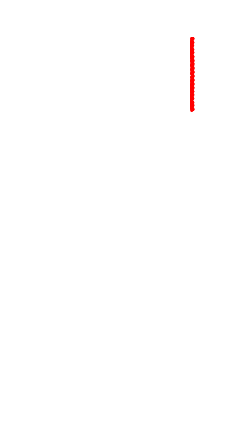

```mathematica
fig6di=Module[
{R=disimr,
sim=disim,
mx,mn,mn2,mx2,smx,ymn,ymx,rmn,rmx,
dist,
lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
{-1,1}]]},
mx=Max[R[[All,1]]];
mn=Min[R[[All,1]]];
ymn=Min[R[[All,3]]];
ymx=Max[R[[All,3]]];
smx=Max[sim[Embedding][[All,1]]];
rmn=Min[disimr[[All,1]]];
rmx=Max[disimr[[All,1]]];
{mn2,mx2}={Min@#,Max@#}&[sim[Embedding][[sim[Index][[1]],1]]];
GraphicsColumn[
{ListPlot[
Map[
{(smx-mn)-(#[[1]]-mn),#[[2]]}&,
{sim[Embedding][[sim[Index][[1]],{1,3}]],
sim[Embedding][[sim[Index][[2]],{1,3}]]},
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->{$ConeColors[[1]],Blue},
PlotMarkers->{{●,2}},
PlotRange->{{-0.05,smx-mn+0.05},{ymn,ymx+0.005}},
ImageSize->3.0*72,
AspectRatio->0.387],
ListPlot[
Map[
{(mx2-mn2)-(#[[1]]-mn2),#[[2]]}&,
sim[Embedding][[sim[Index][[1]],{1,3}]]],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->$ConeColors[[1]],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(mx2-mn2)+0.001},{ymn,ymx+0.005}},
ImageSize->3.0*72,
AspectRatio->0.387],
ListPlot[
Map[
{(rmx-rmn)-(#[[1]]-rmn),#[[2]]}&,
R[[All,{1,3}]]],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->$ConeColors[[1]],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(rmx-rmn)+0.001},{ymn,ymx+0.005}},
ImageSize->3.0*72,
AspectRatio->0.387],
Show[
{Histogram[
Map[((rmx-rmn)-(#-rmn))&,R[[All,1]]],
20,
ChartStyle->Gray,
PlotRange->{{-0.001,(rmx-rmn)+0.001},{0,80}},
Axes->None,
FrameTicks->False,
ImageSize->{3.0,0.2*3.0}*72,
AspectRatio->0.2],
Block[{u,s},
dist=EstimatedDistribution[
Map[((rmx-rmn)-(#-rmn))&,R[[All,1]]],
NormalDistribution[u,s],
{{u,(rmx-rmn)/2},
{s,0.0002}}];
Plot[
PDF[
dist,
t]/40,
{t,-0.001,(rmx-rmn)+0.001},
PlotStyle->Thread[{Dashed,$ConeColors}],
PlotRange->Full]]},
ImagePadding->0]},
Spacings->{0,20},
Alignment->{Left,{Center,Center,Center,Top}},
Epilog->{
lbl["(A)",{0,1},Bold,10],
lbl["Dichromat Full Embedding",{0.1,1},Normal,10],
lbl["(B)",{0,0.71},Bold,10],
lbl["Dichromat L Cone Embedding",{0.1,0.71},Normal,10],
lbl["(C)",{0,0.4},Bold,10],
lbl["Dichromat Flattened L Cone Embedding",{0.1,0.4},Normal,10],
lbl["(D)",{0,0.15},Bold,10],
lbl["Dichromat L Cone Histogram and Fits",{0.1,0.15},Normal,10]}]]
```

### Tetrachromat

#### Load Data/Set Params

```mathematica
tetrasim=First[
Select[
ditetraJavaSims,
And[
#[Suppression]=!=0,
Max[Flatten[#[Retina]]]==4,
#[Ls]==47
]&]];
tetraflat=tetrasim[Flatten];
tetrasimr=Part[
tetraflat,
tetrasim[Flatten,Index][[1]]];
tetrasimg=Part[
tetraflat,
tetrasim[Flatten,Index][[2]]];
tetrasimo=Part[
tetraflat,
tetrasim[Flatten,Index][[3]]];
```

#### How well can a tetrachromat simulation do if we find it a good fit with 3 clusters?

```mathematica
Block[{t,w1,w2,w3,u1,u2,u3,s1,s2,s3,a1,a2,a3},
With[
{zs=tetrasim[Flatten][[All,1]]},
With[
{sdist=SmoothKernelDistribution[zs],
mn=Min[zs],
mx=Max[zs]},
With[
{samp=Table[
{mn+i/100*(mx-mn),PDF[sdist,mn+i/100*(mx-mn)]},
{i,0,100,1}]},
With[
{dist=NonlinearModelFit[
zs,
{PDF[
MixtureDistribution[
{w1,w2,w3},
{SkewNormalDistribution[u1,s1,a1],
SkewNormalDistribution[u2,s2,a2],
SkewNormalDistribution[u3,s3,a3]}],
t],
And[s1>0,s2>0,s3>0]},
{{w1,0.5},{w2,1},{w3,0.25},
{u1,-0.002},{u2,0.001},{u3,0.005},
{s1,0.00001},{s2,0.000005},{s3,0.0002},
{a1,0},{a2,0},{a3,0}},
t]},
With[
{types=Map[
z↦Last[
Ordering[
ReplaceAll[
{w1*PDF[SkewNormalDistribution[u1,s1,a1],z],
w2*PDF[SkewNormalDistribution[u2,s2,a2],z],
w3*PDF[SkewNormalDistribution[u3,s3,a3],z]},
dist["BestFitParameters"]]]],
zs]},
With[
{clusts=TypesToClusters[types]},
MapThread[
N[Length[Intersection[#1,#2]]/Length[#1]]&,
{tetrasim[Flatten,Index],clusts}]]]]]]]]
```

{1.,1.,0.293651}

```mathematica
(* Does it find 3 clusters by itself? *)
Max[Union[tetrasim[ConeTypes]]]==3
```

False

#### How accurate is the classification (per cone type)

```mathematica
tetratypesK3=tetrasim[ConeTypes,ClusterCount->3];
tetratypes=tetrasim[ConeTypes,ClusterCount->3];
```

```mathematica
tetratypes=TypeSimRetina[tetrasim];
```

```mathematica
tetrafret=DeleteCases[
Flatten[Transpose[tetrasim[Retina]]],
Max[Flatten[tetrasim[Retina]]]];
```

```mathematica
MapThread[
Function[{nm,types},
nm->First[
Round[
Sort[
Map[
N[
Table[
{Length[
Intersection[
Flatten@Position[tetrafret,k],
Flatten@Position[Replace[types,#,{1}],k]]],
Length[Flatten@Position[tetrafret,k]]},
{k,Union[tetrafret]}]]&,
Thread[Range[4]->#]&/@Permutations[Range[4]]],
Total[#1[[All,1]]]>Total[#2[[All,1]]]&]]]],
{{"k=3","k=?"},{tetratypesK3,tetratypes}}]
```

{k=3→{{11,125},{42,125},{77,126}},k=?→{{84,125},{0,125},{42,126}}}

{k=3→{{67,125},{20,125},{42,126}},k=?→{{67,125},{20,125},{42,126}}}

```mathematica
20.0/125
```

0.16

#### Figure

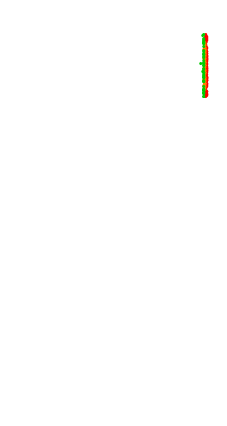

```mathematica
fig6tetra=Module[
{R=tetrasimr,
G=tetrasimg,
O=tetrasimo,
sim=tetrasim,
mx,mn,mn2,mx2,smn,smx,ymn,ymx,
lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
{-1,1}]]},
mx=Max[Join[R,G,O][[All,1]]];
mn=Min[Join[R,G,O][[All,1]]];
{mn2,mx2}={Min@#,Max@#}&[sim[Embedding][[Flatten[sim[Index][[1;;-2]],1],1]]];
smn=Min[sim[Embedding][[All,1]]];
smx=Max[sim[Embedding][[All,1]]];
ymn=Min[sim[Embedding][[All,3]]];
ymx=Max[sim[Embedding][[All,3]]];
GraphicsColumn[
{ListPlot[
Map[
{(smx-smn)-(#[[1]]-smn),#[[2]]}&,
{sim[Embedding][[sim[Index][[1]],{1,3}]],
sim[Embedding][[sim[Index][[2]],{1,3}]],
sim[Embedding][[sim[Index][[3]],{1,3}]],
sim[Embedding][[sim[Index][[4]],{1,3}]]},
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->Append[$ConeColors[[{1,3,2}]],Blue],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(smx-smn)+0.001},{ymn,ymx+0.002}},
ImageSize->3.0*72,
AspectRatio->0.387],
ListPlot[
Map[
{(mx2-mn2)-(#[[1]]-mn2),#[[2]]}&,
{sim[Embedding][[sim[Index][[1]],{1,3}]],
sim[Embedding][[sim[Index][[2]],{1,3}]],
sim[Embedding][[sim[Index][[3]],{1,3}]]},
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->$ConeColors[[{1,3,2}]],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(mx2-mn2)+0.001},{ymn,ymx+0.002}},
ImageSize->3.0*72,
AspectRatio->0.387],
ListPlot[
Map[
{(mx-mn)-(#[[1]]-mn),#[[2]]}&,
{R[[All,{1,3}]],
G[[All,{1,3}]],
O[[All,{1,3}]]},
{2}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Axes->None,
FrameLabel->None,
FrameTicks->False,
PlotStyle->$ConeColors[[{1,3,2}]],
PlotMarkers->{{●,2}},
PlotRange->{{-0.001,(mx-mn)+0.001},{ymn,ymx+0.002}},
ImageSize->3.0*72,
AspectRatio->0.387],
Show[
{Histogram[
(mx-mn)-(
Join[
R[[All,1]],
G[[All,1]],
O[[All,1]]]-mn),
40,
ChartStyle->Gray,
PlotRange->{{-0.001,mx-mn+0.001},{0,175}},
Axes->None,
FrameTicks->False,
ImageSize->{3.0,0.2*3.0}*72,
AspectRatio->0.2],
Block[{dists},
TypeSimRetina[tetrasim,DistHook->((dists=#)&)];
Plot[
Evaluate[
MapThread[
{w,d}↦w*PDF[d,mx-t]/5,
Transpose[
SortBy[
Transpose[List@@dists],
-#[[2,1]]&]]]],
{t,-0.001,(mx-mn)+0.001},
PlotStyle->(Thread[{Dashed,{Darker@Green,Red}}]),
PlotRange->Full]]},
ImagePadding->0]},
Spacings->{0,20},
Alignment->{Left,{Center,Center,Center,Top}},
Epilog->{
lbl["(E)",{0,1},Bold,10],
lbl["Tetrachromat Full Embedding",{0.1,1},Normal,10],
lbl["(F)",{0,0.71},Bold,10],
lbl["Tetrachromat L, A, and M Cone",{0.1,0.71},Normal,10],
lbl["Embedding",{0.1,0.68},Normal,10],
lbl["(G)",{0,0.4},Bold,10],
lbl["Tetrachromat Flattened L, A, and M",{0.1,0.4},Normal,10],
lbl["Cone Embedding",{0.1,0.37},Normal,10],
lbl["(H)",{0,0.15},Bold,10],
lbl["Tetrachromat L, A, and M Cone Histogram",{0.1,0.15},Normal,10],
lbl["and Fits",{0.1,0.12},Normal,10]}]]
```

### Combined

```mathematica
fig6=Graphics[
{Inset[fig6di,ImageScaled[{0,0}],ImageScaled[{0,0}]],
Inset[fig6tetra,ImageScaled[{1,0}],ImageScaled[{1,0}]]},
ImageSize->{6.75,5.5}*72,
ImagePadding->8*72]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figditetra.pdf",fig6,"PDF"];
```

### 3D Figures

#### A: Dichromat Full Embedding

```mathematica
fig6a3d=Module[
{μ=Mean/@Transpose[fig4sim[Embedding]],
em=Map[disim[Embedding][[#]]&,disim[Index][[1;;2]]],
mn,mx,
r=4},
mn=Min/@Transpose[Flatten[em,1]];
mx=Max/@Transpose[Flatten[em,1]];
em=Map[
{(#[[1]]-mn[[1]])/(mx[[1]]-mn[[1]]),
(#[[2]]-mn[[2]])/(mx[[2]]-mn[[2]]),
(#[[3]]-mn[[3]])/(mx[[3]]-mn[[3]])}&,
em,
{2}];
Table[
With[
{s=Mod[t,1]},
Image[
SpheresPlot3D[
em,
PlotStyle->{$ConeColors[[1]],Blue},
PointSize->0.015,
ViewPoint->If[t<1,
r*{Cos[s*2*Pi],Sin[s*2*Pi],0},
r*{Cos[s*2*Pi],0,Sin[s*2*Pi]}],
ViewCenter->{0.5,0.5,0.5},
ViewAngle->Pi/10,
ViewVertical->If[t<1,
{0,0,1},
{Cos[(s+0.02)*2*Pi],0,Sin[(s+0.02)*2*Pi]}-{Cos[s*2*Pi],0,Sin[s*2*Pi]}]]]],
{t,0,1.99,0.02}]];
```

```mathematica
Manipulate[
fig6a3d[[k]],
{k,1,Length@fig4a3d,1}]
```

```mathematica
Export["~/Desktop/dichromat-animated-embedding-full.gif",fig6a3d,"GIF",ImageResolution->300,
"DisplayDurations"->0.15];
```

#### B: Dichromat Zoomed Embedding

```mathematica
fig6b3d=Module[
{μ=Mean/@Transpose[fig4sim[Embedding]],
em=Map[disim[Embedding][[#]]&,disim[Index][[{1}]]],
mn,mx,
r=4},
mn=Min/@Transpose[Flatten[em,1]];
mx=Max/@Transpose[Flatten[em,1]];
em=Map[
{(#[[1]]-mn[[1]])/(mx[[1]]-mn[[1]]),
(#[[2]]-mn[[2]])/(mx[[2]]-mn[[2]]),
(#[[3]]-mn[[3]])/(mx[[3]]-mn[[3]])}&,
em,
{2}];
Table[
With[
{s=Mod[t,1]},
Image[
SpheresPlot3D[
em,
PlotStyle->{$ConeColors[[1]]},
PointSize->0.015,
ViewPoint->If[t<1,
r*{Cos[s*2*Pi],Sin[s*2*Pi],0},
r*{Cos[s*2*Pi],0,Sin[s*2*Pi]}],
ViewCenter->{0.5,0.5,0.5},
ViewAngle->Pi/10,
ViewVertical->If[t<1,
{0,0,1},
{Cos[(s+0.02)*2*Pi],0,Sin[(s+0.02)*2*Pi]}-{Cos[s*2*Pi],0,Sin[s*2*Pi]}]]]],
{t,0,1.99,0.02}]];
```

```mathematica
Manipulate[
fig6b3d[[k]],
{k,1,Length@fig4a3d,1}]
```

```mathematica
Export["~/Desktop/dichromat-animated-embedding-lm.gif",fig6b3d,"GIF",ImageResolution->300,
"DisplayDurations"->0.15];
```

#### C: Tetrachromat Full Embedding

```mathematica
fig6c3d=Module[
{em=Map[tetrasim[Embedding][[#]]&,tetrasim[Index][[1;;4]]],
mn,mx,
r=4},
mn=Min/@Transpose[Flatten[em,1]];
mx=Max/@Transpose[Flatten[em,1]];
em=Map[
{(#[[1]]-mn[[1]])/(mx[[1]]-mn[[1]]),
(#[[2]]-mn[[2]])/(mx[[2]]-mn[[2]]),
(#[[3]]-mn[[3]])/(mx[[3]]-mn[[3]])}&,
em,
{2}];
Table[
With[
{s=Mod[t,1]},
Image[
SpheresPlot3D[
em,
PlotStyle->{$ConeColors[[1]],$ConeColors[[3]],$ConeColors[[2]],Blue},
PointSize->0.01,
ViewPoint->If[t<1,
r*{Cos[s*2*Pi],Sin[s*2*Pi],0},
r*{Cos[s*2*Pi],0,Sin[s*2*Pi]}],
ViewCenter->{0.5,0.5,0.5},
ViewAngle->Pi/10,
ViewVertical->If[t<1,
{0,0,1},
{Cos[(s+0.02)*2*Pi],0,Sin[(s+0.02)*2*Pi]}-{Cos[s*2*Pi],0,Sin[s*2*Pi]}]]]],
{t,0,1.99,0.02}]];
```

```mathematica
Manipulate[
fig6c3d[[k]],
{k,1,Length@fig4a3d,1}]
```

```mathematica
Export["~/Desktop/tetrachromat-animated-embedding-full.gif",fig6c3d,"GIF",ImageResolution->300,
"DisplayDurations"->0.15];
```

#### B: Zoomed Embedding

```mathematica
fig6d3d=Module[
{μ=Mean/@Transpose[fig4sim[Embedding]],
em=Map[tetrasim[Embedding][[#]]&,tetrasim[Index][[1;;3]]],
mn,mx,
r=4},
mn=Min/@Transpose[Flatten[em,1]];
mx=Max/@Transpose[Flatten[em,1]];
em=Map[
{(#[[1]]-mn[[1]])/(mx[[1]]-mn[[1]]),
(#[[2]]-mn[[2]])/(mx[[2]]-mn[[2]]),
(#[[3]]-mn[[3]])/(mx[[3]]-mn[[3]])}&,
em,
{2}];
Table[
With[
{s=Mod[t,1]},
Image[
SpheresPlot3D[
em,
PlotStyle->$ConeColors[[{1,3,2}]],
PointSize->0.015,
ViewPoint->If[t<1,
r*{Cos[s*2*Pi],Sin[s*2*Pi],0},
r*{Cos[s*2*Pi],0,Sin[s*2*Pi]}],
ViewCenter->{0.5,0.5,0.5},
ViewAngle->Pi/10,
ViewVertical->If[t<1,
{0,0,1},
{Cos[(s+0.02)*2*Pi],0,Sin[(s+0.02)*2*Pi]}-{Cos[s*2*Pi],0,Sin[s*2*Pi]}]]]],
{t,0,1.99,0.02}]];
```

```mathematica
Manipulate[
fig6d3d[[k]],
{k,1,Length@fig6d3d,1}]
```

```mathematica
Export["~/Desktop/tetrachromat-animated-embedding-lm.gif",fig6d3d,"GIF",ImageResolution->300,
"DisplayDurations"->0.15];
```

## Figure S1: Mosaic Accuracy

### Load Data/Set Params

```mathematica
fig6sim=DeclareJavaSimulation[Samples->2000000];
```

### Figure

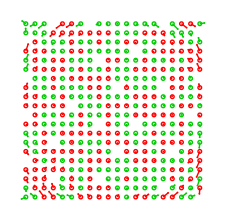

```mathematica
fig6=Block[{xscale,yscale,x0,y0,θ},
Module[
{em=Part[
fig6sim[Embedding],
Flatten[fig6sim[Index][[{1,2}]]],
{2,3}],
correct=Flatten[fig6sim[Index2D][[{1,2}]],1],
sol},
sol=FindMinimum[
{Total[
MapThread[
EuclideanDistance,
{Map[
#+{x0,y0}&,
Dot[
em,
N[{{xscale*Cos[θ],-yscale*Sin[θ]},
{xscale*Sin[θ],yscale*Cos[θ]}}]]],
correct}]]},
{{xscale,85},{yscale,85},{x0,10.5},{y0,10.5},{θ,60*Pi/180}},
AccuracyGoal->4
][[2]];
Module[
{arranged=ReplaceAll[
Map[
#+{x0,y0}&,
Dot[
em,
N[{{xscale*Cos[θ],-yscale*Sin[θ]},
{xscale*Sin[θ],yscale*Cos[θ]}}]]],
sol],
nred=Length[fig6sim[Index][[1]]]},
Graphics[
MapThread[
Function[{arrangedSubset,correctSubset,color},
Reap[
Sow[color];
MapThread[
Sow[
{Circle[#2,0.2],
Line[{#2,#1}],
Disk[#1,0.1]}]&,
{arrangedSubset,correctSubset}]
][[2,1]]],
{{arranged[[1;;nred]],arranged[[nred+1;;All]]},
{correct[[1;;nred]],correct[[nred+1;;All]]},
$ConeColors[[1;;2]]}],
ImageSize->3.15*72]]]]
```

```mathematica
Export[$FiguresDir<>"/figSmosaic.pdf",fig6,"PDF"];
```

## Figure S2: Individual Simulation Results

### Percentage classified correctly if k=2

```mathematica
figSeachsimcorrect=Map[
PlotSizeCondition,
{fig4dat1,fig4dat2,fig4dat3}]
```

{-Graphics-,-Graphics-,-Graphics-}

### Number of classes found in each simulation

```mathematica
figSeachsimclasses=Map[
PlotKCorrect[#,Min->1,Max->3]&,
{fig4types1,fig4types2,fig4types3}]
```

{-Graphics-,-Graphics-,-Graphics-}

### Combined

```mathematica
figSeachsim=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
Join[
MapThread[
Inset[#1,ImageScaled[{0,#2}],ImageScaled[{0,0}]]&,
{figSeachsimcorrect,
{0,1/3,2/3}}],
MapThread[
Inset[#1,ImageScaled[{0.5,#2}],ImageScaled[{0,0}]]&,
{figSeachsimclasses,
{0,1/3,2/3}}]],
ImagePadding->6.5*72,
ImageSize->{6.5,6.5}*72,
Epilog->{
lbl["(a)",{0,0.98},Bold,10],
lbl["(b)",{0,0.65},Bold,10],
lbl["(c)",{0,0.315},Bold,10],
lbl["Simulation 1",{0.05,0.98},Normal,10],
lbl["Simulation 2",{0.05,0.65},Normal,10],
lbl["Simulation 3",{0.05,0.315},Normal,10],

lbl["Fraction Correctly Classified",{0.09,0.95},Normal,10],
lbl["Number of Cone Classses Found",{0.57,0.95},Normal,10],
lbl["Fraction Correctly Classified",{0.09,0.62},Normal,10],
lbl["Number of Cone Classses Found",{0.57,0.62},Normal,10],
lbl["Fraction Correctly Classified",{0.09,0.285},Normal,10],
lbl["Number of Cone Classses Found",{0.57,0.285},Normal,10],
Inset[
Graphics[{White,Rectangle[{0,0},{3,40}]}],
ImageScaled[{0.52,0}],
ImageScaled[{0.5,0}]],
Inset[
Graphics[{White,Rectangle[{0,0},{3,40}]}],
ImageScaled[{0.52,0.92}],
ImageScaled[{0.5,1}]]}]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSeachsim.pdf",figSeachsim,"PDF"];
```

## Figure S3: Performance w/o Surround

### Figure S3A: Accuracy

```mathematica
figS3dat=ParallelMap[
ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]&,
Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==0,
#[Suppression]==0,
#[RetinaSize]==20,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]],
{2}];
```

```mathematica
figS3a=PlotSizeCondition[figS3dat]
```

-Graphics-

### Figure S2B: Where k=2

```mathematica
figS3btypes=Map[
#[ConeTypes]&,
Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==0,
#[Suppression]==0,
#[RetinaSize]==20,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]],
{2}];
```

```mathematica
figS3b=PlotKCorrect[
Map[
Length[Union[#]]&,
figS3btypes,
{2}],
Min->1,
Max->3]
```

-Graphics-

### Combined

```mathematica
figS3=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS3a,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS3b,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(a)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(b)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSaccuracy-nosurround.pdf",figS3,"PDF"];
```

## Figure S4: Samples Versus Accuracy

### Prep Data

```mathematica
samplesJavaSims:=(
samplesJavaSims=Map[
DeclareJavaSimulation[ParseJavaSimFilename[#]]&,
FileNames[$JavaSimDir<>"/samples/*.bin"]];
samplesJavaSims);
```

```mathematica
samplesSims=SortBy[
Select[
samplesJavaSims,
sim↦And[
sim[RetinaSize]==20,
sim[MΛMax]==530||sim[MΛMax]==540||sim[MΛMax]==550,
sim[Suppression]=!=0,
sim[Ls]==19||sim[Ls]==47||sim[Ls]==75]],
sim↦sim[Samples]];
```

```mathematica
samplesdat=Map[
Sort[#,#1[Samples]<#2[Samples]&]&,
Split[
Sort[
Select[
samplesSims,
#[Suppression]=!=0&&#[Samples]≤2000000&],
OrderedQ[{{#1[MΛMax],#1[Ls]},{#2[MΛMax],#2[Ls]}}]&],
#1[MΛMax]==#2[MΛMax]&&#1[Ls]==#2[Ls]&]];
```

### Figure

#### Legend

```mathematica
figS4legend=Graphics[
Join[
MapThread[
{Black,
Switch[#1[Ls],
19,Dotted,
47,Dashing[{}],
75,Dashed],
Line[{{-0.5,#2},{1.5,#2}}],
Text[
Style[
StringJoin[
"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M) = ",
ToString[Switch[#[Ls],19,-4,47,0,75,4]]],
FontFamily->"Arial",
FontSize->8],
{1.7,#2},
{-1,0}]}&,
{samplesdat[[1;;3,1]],
Range[3]}],
MapThread[
{Switch[#[MΛMax],
530,Blue,
540,$ConeColors[[2]],
550,Red],
Inset[
Switch[#[MΛMax],
530,●,
540,◆,
550,▲],
{0.5,#2},
ImageScaled[{0.5,0.5}]],
Black,
Text[
Style[
StringJoin[
"M \!\(\*SubscriptBox[\(λ\),\(max\)]\) = ",
ToString[#1[MΛMax]]],
FontFamily->"Arial",
FontSize->8],
{1.7,#2},
{-1,0}]}&,
{samplesdat[[1;;All;;3,1]],
Range[4,6]}]],
ImageSize->{1.1,1}*72]
```

-Graphics-

#### Plot

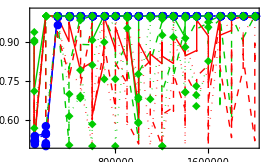

```mathematica
figS4plot=ListPlot[
Map[
{#[Samples],ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]}&,
samplesdat,
{2}],
PlotRange->{0.5,1.02},
PlotStyle->Map[
{Switch[#[MΛMax],
530,Blue,
540,$ConeColors[[2]],
550,Red],
Switch[#[Ls],
19,Dotted,
47,Dashing[{}],
75,Dashed]}&,
samplesdat[[All,1]]],
PlotMarkers->Map[
{Switch[#[MΛMax],
530,●,
540,◆,
550,▲]}&,
samplesdat[[All,1]]],
Joined->True,
BaseStyle->Directive[10,FontFamily->"Arial"],
ImageSize->{3.75,2.25}*72,
AspectRatio->0.6,
Axes->None,
Frame->{{True,False},{True,False}},
FrameTicks->{
{True,False},
{True,False}},
FrameLabel->{{"Fraction Correcrly Classified",None},{"Number of Simulated Image Patches",None}}]
```

```mathematica
Join[
Table[
{10^s,Superscript["10",ToString[s]],{0.02,0}},
{s,3,7}],
Flatten[
Table[
{x*10^s,Null,{0.01,0}},
{s,3,7},
{x,2,9}],
1]],
```

#### Combined

```mathematica
figS4=Graphics[
{Inset[
figS4plot,
ImageScaled[{0,1}],
ImageScaled[{0,1}]],
Inset[
figS4legend,
ImageScaled[{1,0.5}],
ImageScaled[{1,0.5}]]},
ImagePadding->2000,
ImageSize->{4.5,2.35}*72]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSsamples.png",figS4,"PNG",ImageResolution->400];
```

## Figure S5: Performance of 10 x 10 and 15 x 15

### Figure S5A: 10 x 10 Accuracy

```mathematica
figS5adat=Map[
ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]&,
Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==0,
#[Suppression]==0,
#[RetinaSize]==10,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]],
{2}];
```

```mathematica
figS5a=PlotSizeCondition[figS5adat]
```

-Graphics-

### Figure S5C: 10 x 10 where k=2

```mathematica
figS5atypes=Map[
#[ConeTypes]&,
Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==0,
#[Suppression]==0,
#[RetinaSize]==10,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]],
{2}];
```

```mathematica
figS5c=PlotKCorrect[
Map[
Length[Union[#]]&,
figS5atypes,
{2}],
Min->1,
Max->3]
```

-Graphics-

### Figure S5B: 15 x 15 Accuracy

```mathematica
figS5bdat=Map[
ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]&,
Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==0,
#[Suppression]==0,
#[RetinaSize]==15,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]],
{2}];
```

```mathematica
figS5b=PlotSizeCondition[figS5bdat]
```

-Graphics-

### Figure S5D: 15 x 15 where k=2

```mathematica
figS5dtypes=Map[
#[ConeTypes]&,
Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==0,
#[Suppression]==0,
#[RetinaSize]==15,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]],
{2}];
```

```mathematica
figS5d=PlotKCorrect[
Map[
Length[Union[#]]&,
figS5dtypes,
{2}],
Min->1,
Max->3]
```

-Graphics-

### Combined

```mathematica
figS5=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]],
A=Graphics[
{Inset[figS5a,ImageScaled[{0,0}],ImageScaled[{0,0}]]},
ImageSize->{2.75,2.05}*72,
ImagePadding->4*72],
C=Graphics[
{Inset[figS5c,ImageScaled[{0,0}],ImageScaled[{0,0}]]},
ImageSize->{2.75,2.05}*72,
ImagePadding->4*72]},
Graphics[
{Inset[figS5b,ImageScaled[{0.6025,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS5d,ImageScaled[{0.6025,0.25}],ImageScaled[{0.5,0.5}]],
Inset[C,ImageScaled[{0.25,0.25}],ImageScaled[{0.5,0.5}]],
Inset[A,ImageScaled[{0.25,0.75}],ImageScaled[{0.5,0.5}]]},
ImageSize->{6,4.35}*72,
ImagePadding->6*72,
Epilog->List[
lbl["(a)",{0.05,0.965},Bold,10],
lbl["Fraction Correctly Classified",{0.1,0.965},Normal,10],
lbl["(b)",{0.05,0.465},Bold,10],
lbl["Number of Cone Classes Found",{0.1,0.465},Normal,10],
lbl["10×10",{0.24,0.935},Normal,10],
lbl["15×15",{0.555,0.935},Normal,10],
lbl["10×10",{0.24,0.435},Normal,10],
lbl["15×15",{0.555,0.435},Normal,10]]]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSaccuracy-10-15.pdf",figS5,"PDF"];
```

## Figure S6: Performance w/o Man-made Images

### Figure S6A: Accuracy

```mathematica
figS6dat=Map[
ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]&,
Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
wmmJavaSims,
And[
#[Run]==1,
#[Suppression]=!=0,
#[RetinaSize]==20]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]],
{2}];
```

```mathematica
figS6a=PlotSizeCondition[figS6dat]
```

-Graphics-

### Figure S2B: Where k=2

```mathematica
figS6types=Map[
#[ConeTypes]&,
Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
wmmJavaSims,
And[
#[Run]==1,
#[Suppression]=!=0,
#[RetinaSize]==20]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]],
{2}];
```

```mathematica
figS6b=PlotKCorrect[
Map[
If[Length[Union[#]]==2,2,1]&,
figS6types,
{2}],
Min->1,
Max->3]
```

-Graphics-

### Combined

```mathematica
figS6=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS6a,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS6b,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(a)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(b)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSaccuracy-nomanmade.pdf",figS6,"PDF"];
```

## Figure S7: Performance with blur

```mathematica
blurSims=Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
blurJavaSims,
And[
#[Suppression]=!=0,
#[RetinaSize]==20,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]];
```

### Figure S7A: Accuracy

```mathematica
figS7dat=ParallelMap[
ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]&,
blurSims,
{2}];
```

```mathematica
figS7a=PlotSizeCondition[figS7dat,Label->blurSims]
```

-Graphics-

### Figure S2B: Where k=2

```mathematica
figS7types=Map[
#[ConeTypes]&,
blurSims,
{2}];
```

```mathematica
figS7b=PlotKCorrect[
Map[
If[Length[Union[#]]==2,2,1]&,
figS7types,
{2}],
Min->1,
Max->3,
Label->blurSims]
```

-Graphics-

### Combined

```mathematica
figS7=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS7a,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS7b,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(a)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(b)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSaccuracy-blur.png",figS7,"PNG",ImageResolution->400];
```

## Figure S8: Performance with spectrally-spaced M cones

```mathematica
specspaceSims=Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
specspaceJavaSims,
And[
#[Suppression]=!=0,
#[RetinaSize]==20,
#[MΛMax]==513,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]];
```

### Figure S8A: Accuracy

```mathematica
figS8dat=ParallelMap[
ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]&,
specspaceSims,
{2}];
```

```mathematica
figS8dat
```

{{1}}

### Figure S8B: Where k=2

```mathematica
figS8types=Map[
#[ConeTypes]&,
specspaceSims,
{2}];
```

### Combined

```mathematica
figS8=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS8a,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS8b,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(a)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(b)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSaccuracy-specspace.png",figS8,"PNG",ImageResolution->400];
```

## Figure S9: Performance with LM-dichromats

```mathematica
lmonlySims=Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
lmonlyJavaSims,
And[
#[Suppression]=!=0,
#[RetinaSize]==20,
#[Samples]==5000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]];
```

### Figure S8A: Accuracy

```mathematica
figS9dat=Map[
ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]&,
lmonlySims,
{2}];
```

```mathematica
Scan[(#[MΛMax]="")&,lmonlySims,{2}];
figS9a=PlotSizeCondition[figS9dat,Label->lmonlySims]
```

-Graphics-

### Figure S8B: Where k=2

```mathematica
figS9types=Map[
#[ConeTypes]&,
lmonlySims,
{2}];
```

```mathematica
figS9b=PlotKCorrect[
Map[
Length[Union[#]]&,
figS9types,
{2}],
Min->1,
Max->3,
Label->lmonlySims]
```

-Graphics-

### Combined

```mathematica
figS10=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS9a,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS9b,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(a)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(b)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSaccuracy-lmonly.png",figS10,"PNG",ImageResolution->400];
```

## Figure S10: Performance in the periphery (to be deleted?)

```mathematica
peripherySims=Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
peripheryJavaSims,
And[
#[Suppression]=!=0,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]];
```

### Figure S10A: Accuracy

```mathematica
figS10dat=ParallelMap[
ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]&,
peripherySims,
{2}];
```

```mathematica
Scan[(#[MΛMax]="")&,peripherySims,{2}];
figS8a=PlotSizeCondition[figS10dat,Label->peripherySims]
```

### Figure S8B: Where k=2

```mathematica
figS10types=Map[
#[ConeTypes]&,
peripherySims,
{2}];
```

```mathematica
figS10b=PlotKCorrect[
Map[
Length[Union[#]]&,
figS10types,
{2}],
Min->1,
Max->3,
Label->peripherySims]
```

-Graphics-

### Combined

```mathematica
figS8=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS8a,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS8b,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(a)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(b)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSaccuracy-specspace.png",figS8,"PNG",ImageResolution->400];
```

## Figure S11: MDS Solution Effectiveness

```mathematica
mdssim=DeclareJavaSimulation[Samples->2000000];
```

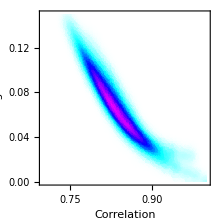

```mathematica
figS10=With[
{R=mdssim[Correlation],
D=Outer[EuclideanDistance,mdssim[Embedding],mdssim[Embedding],1,1]},
With[
{pts=Transpose[
dbg=Map[
M↦Select[Flatten[UpperTriangularize[M]],#=!=0&],
{R,D}]]},
SmoothDensityHistogram[
Select[pts,#[[1]]>=0.7&&#[[2]]<=0.15&],
ColorFunction->(val↦Blend[{White,Cyan,Blue,Magenta},val]),
Mesh->True,
Frame->{{True,False},{True,False}},
Axes->None,
PlotRange->{{0.7,1},{0,0.15},Full},
FrameLabel->{{"Embedding Distance",None},{"Correlation",None}},
ImageSize->3.05*72,
AspectRatio->1,
BaseStyle->Directive[10,FontFamily->"Arial"]]]]
```

```mathematica
Export[$FiguresDir<>"/figSdist-vs-corr.png",figS10,"PNG",ImageResolution->400];
```

## Figure S12: Performance with noise

```mathematica
noiseSims=Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
noiseJavaSims,
And[
#[Suppression]=!=0,
#[RetinaSize]==20,
#[Samples]==2500000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]];
```

### Figure S11A: Accuracy

```mathematica
figS11dat=Map[
ScoreTypes[#,ConeTypes->#[ConeTypes,ClusterCount->2]]&,
noiseSims,
{2}];
```

```mathematica
figS11a=PlotSizeCondition[figS11dat,Label->noiseSims]
```

-Graphics-

### Figure S11B: Where k=2

```mathematica
figS11types=Map[
#[ConeTypes]&,
noiseSims,
{2}];
```

```mathematica
figS11b=PlotKCorrect[
Map[
Length[Union[#]]&,
figS11types,
{2}],
Min->1,
Max->3,
Label->noiseSims]
```

-Graphics-

### Combined

```mathematica
figS11=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
ImageScaled[coord],
ImageScaled[{0,0}]]]},
Graphics[
{Inset[figS11a,ImageScaled[{0.5,0.75}],ImageScaled[{0.5,0.5}]],
Inset[figS11b,ImageScaled[{0.5,0.25}],ImageScaled[{0.5,0.5}]]},
ImageSize->{3.25,4.25}*72,
ImagePadding->5*72,
Epilog->List[
lbl["(a)",{0.05,0.95},Bold,10],
lbl["Fraction Correctly Classified",{0.15,0.95},Normal,10],
lbl["(b)",{0.05,0.45},Bold,10],
lbl["Number of Cone Classes Found",{0.15,0.45},Normal,10]]]]
```

-Graphics-

```mathematica
Export[$FiguresDir<>"/figSaccuracy-noise.png",figS11,"PNG",ImageResolution->400];
```

## Export 3D Rotating Embeddings

```mathematica
sims3d=Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allJavaSims,
And[
#[Run]==0,
#[Suppression]=!=0,
#[RetinaSize]==20,
#[Samples]==2000000]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]];
```

```mathematica
ExportRotatingImages[sims_List,type:(Full|LM|Flatten)]:=Map[
sim↦ExportRotatingImage[
StringJoin[
$FiguresDir,"/3D/",
Switch[type,Full,"full",LM,"zoom",Flatten,"flat"],
"_Mlmax=",ToString[sim[MΛMax]],
"_LM=",
If[sim[Ls]==94,
"L-M=1-0",
StringJoin[
"_L-M=",
ToString[Max[{1,2^Round[Log[2,sim[Ls]/(94-sim[Ls])]]}]],
"-",
ToString[Max[{1,2^Round[Log[2,(94-sim[Ls])/sim[Ls]]]}]]]]],
sim,
type],
sims,
{2}];
```

```mathematica
ExportRotatingImages[sims3d,Full];
```

$Aborted

```mathematica
ExportRotatingImages[sims3d,LM];
```

## Deprecated

### Figure 3

#### Old Version

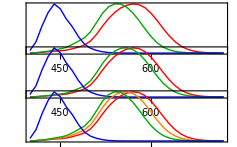

```mathematica
fig3old=GraphicsColumn[
{ListPlot[
spectra,
Joined->True,
AspectRatio->0.25,
PlotStyle->{Red,Hue[1/3,1,2/3],Blue},
DataRange->{400,720},
LabelStyle->Directive[10,FontFamily->"Arial",FontColor->White],
Frame->{{True,False},{True,False}},
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->None,
ImageSize->3.25*72],
ListPlot[
tetraspectra[[{1,2,4}]],
Joined->True,
AspectRatio->0.25,
PlotStyle->{Red,Hue[1/3,1,2/3],Blue},
DataRange->{400,720},
LabelStyle->Directive[10,FontFamily->"Arial",FontColor->White],
Frame->{{True,False},{True,False}},
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->None,
ImageSize->3.25*72],
ListPlot[
tetraspectra,
Joined->True,
AspectRatio->0.25,
PlotStyle->{Red,Orange,Hue[1/3,1,2/3],Blue},
DataRange->{400,720},
LabelStyle->Directive[10,FontFamily->"Arial"],
Frame->{{True,False},{True,False}},
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->None,
ImageSize->3.25*72],
Graphics[
{Text[
Style[
"Wavelength (nm)",
FontFamily->"Arial",
FontSize->10],
{0,0},
{0,0}]},
ImageSize->{3.25*72,0.35*72}]},
Center,
-15,
ImageSize->3.3*72,
Epilog->List[
Text[
Style[
"Spectral Sensitivity",
FontFamily->"Arial",
FontSize->10],
Scaled[{0.11,0.7}],
{0,0},
{0,1}],
Text[
Style[
"(A)",
FontFamily->"Arial",
FontSize->10,
FontWeight->Bold],
Scaled[{0.22,1.15}],
{0,0}],
Text[
Style[
"(B)",
FontFamily->"Arial",
FontSize->10,
FontWeight->Bold],
Scaled[{0.22,0.825}],
{0,0}],
Text[
Style[
"(C)",
FontFamily->"Arial",
FontSize->10,
FontWeight->Bold],
Scaled[{0.22,0.525}],
{0,0}]
]]
```

```mathematica
Export[NotebookDirectory[]<>"figspectra.pdf",fig2,"PDF"];
```

#### 3D: PC1

```mathematica
{pc1Plot,pc1PlotMin,pc1PlotMax}=Module[
{r=Scaled[0.5/fig3sim[RetinaSize]],
pc1=PrincipalComponents[fig3sim[Correlation]][[All,1]],
mn,mx,tmp},
{mn,mx}={Min[#],Quantile[#,3/4]}&[
Part[
pc1,
Join[
fig3sim[Index][[1]],
fig3sim[Index][[1]]]]];
tmp=FindDivisions[{mn,mx},3];
mn=First@tmp;mx=Last@tmp;
{Graphics[
MapIndexed[
Function[{val,idx},
{Which[
MemberQ[fig3sim[Index][[3]],idx],Null,
val<0,Black,
val>1,White,
True,Blend[{Black,White},val]],
Disk[idx,r]}],
Transpose[
Partition[
(pc1-mn)/(mx-mn),
fig3sim[RetinaSize]]],
{2}],
ImageSize->1*72,
AspectRatio->1],
mn,mx}];
pc1Plot
```

-Graphics-

#### 3E: Full Correlation Matrix

```mathematica
fullcorPlot = ArrayPlot[fig3sim[Correlation], 
   ColorFunctionScaling -> False, ColorFunction -> 
    (Which[#1 < 0, Purple, #1 < 0.75, Black, #1 > 1, White, 
      True, Blend[{Black, White}, (#1 - 0.75)/0.25]] & ), 
   BaseStyle -> Directive[10, FontFamily -> "Arial"], 
   ImageSize -> 1*72, AspectRatio -> 1, 
   DataReversed -> True, LabelStyle -> Purple, Frame -> None]
```

-Graphics-

### Figure 4

#### 4A: Full Embedding

```mathematica
fullEmPlot=Block[{x,y,z},
Graphics3D[
MapThread[
{#1,
Map[
Sphere[#*{2,1,1},0.005]&,
#2]}&,
{Append[$ConeColors[[1;;2]],Blue],
Table[
fig4sim[Embedding][[fig4sim[Index][[k]]]],
{k,1,3}]}],
Boxed->False,
Axes->{True,False,True},
AxesEdge->{{1,-1},None,{-1,1}},
BaseStyle->Directive[10,FontFamily->"Arial"],
Ticks->False,
AxesLabel->{x,y,z},
ViewPoint->{-0.2252134658938481,-3.376149790448013,0.029857783540041215},ViewVertical->{-0.04405500836033276,-1.5562940779074965,3.8036049732616097},
ImageSize->3.25*72,
AspectRatio->0.5]]
```

-Graphics3D-

#### 4B: Zoomed Embedding

```mathematica
zoomedEmPlot=Block[{x,y,z},
Module[
{rem=fig4sim[Embedding][[fig4sim[Index][[1]]]],
gem=fig4sim[Embedding][[fig4sim[Index][[2]]]],
rng},
rng={Min@#,Max@#}&/@Transpose[Join[rem,gem]];
rem=Transpose[
MapThread[
(#1-#2[[1]])/(#2[[2]]-#2[[1]])&,
{Transpose[rem],rng}]];
gem=Transpose[
MapThread[
(#1-#2[[1]])/(#2[[2]]-#2[[1]])&,
{Transpose[gem],rng}]];
Graphics3D[
MapThread[
{#1,
Map[
Sphere[#*{2.5,1,1},0.01]&,
#2]}&,
{$ConeColors[[1;;2]],
{rem,gem}}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Boxed->False,
Axes->{True,False,True},
AxesLabel->{x,y,z},
Ticks->False,
ViewPoint->{-0.43067562612135424,-3.3154084834962934,0.5220968230374339},ViewVertical->{-0.08663068651391058,-1.2391970796464065,2.1265908205948594},
ImageSize->3.25*72,
AspectRatio->0.5]]]
```

-Graphics3D-

#### 4C: Flattened Embedding

```mathematica
flatEmPlot=Module[
{em,r,g},
{em,r,g}=Import[$ExportedDir<>"/flattened_em.mat"];
Graphics3D[
MapThread[
{#1,
Map[
Sphere[#*{2.5,1,1},0.01]&,
#2]}&,
{$ConeColors[[1;;2]],
{Reverse/@em[[Flatten@r]],
Reverse/@em[[Flatten@g]]}}],
BaseStyle->Directive[10,FontFamily->"Arial"],
Boxed->False,
Axes->{True,False,True},
AxesLabel->{x,y,z},
Ticks->False,
ViewPoint->{-0.43067562612135424,-3.3154084834962934,0.5220968230374339},ViewVertical->{-0.08815138204128171,-1.1673053599085061,2.0060682426298},
ImageSize->3.25*72,
AspectRatio->0.5]]
```

-Graphics3D-

#### 4D: Histogram

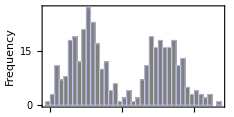

```mathematica
histPlot=Block[{x},
Histogram[
fig4sim[Flatten][[All,3]],
40,
Axes->None,
ChartStyle->Gray,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Frequency",None},{None,None}},
BaseStyle->Directive[10,FontFamily->"Arial"],
AspectRatio->0.5,
ImageSize->3.25*72]]
```

#### Combined

```mathematica
fig4=Module[
{lbl=Function[{txt,coord,bld,sz},
Text[
Style[
txt,
FontFamily->"Arial",
FontSize->sz,
FontWeight->bld],
Scaled[coord],
{0,0}]]},
GraphicsColumn[
{fullEmPlot,zoomedEmPlot,flatEmPlot,histPlot},
Epilog->List[
lbl["(A)",{0.075,1.1},Bold,10],
lbl["(B)",{0.075,0.775},Bold,10],
lbl["(C)",{0.075,0.445},Bold,10],
lbl["(D)",{0.075,0.15},Bold,10]]]]
```

-Graphics-

### Figure 5

```mathematica
fig5b=GraphicsRow[
{ArrayPlot[
MapThread[
(#1-1)+3*(#2-1)&,
Map[
Reverse[
Replace[
#,
Rule[_,types_List]:>Length[Union[types]],
{2}]]&,
Map[
Split[
Sort[
#,
OrderedQ[{#1[[1]],#2[[1]]}]&],
#1[[1,1]]==#2[[1,1]]&]&,
Flatten[
Reap[
MapThread[
Function[{sim,types},
If[sim[Suppression]==10,
Sow[
{sim[MΛMax],sim[Ls]}->types,
sim[Run]]]],
{allSims,fig5types}],
{1,2}
][[2]],
1]]]],
ImageSize->{(3.25-0.85),2.05}*72,
AspectRatio->0.7,
BaseStyle->Directive[10,FontFamily->"Arial"],
FrameLabel->{
{"\!\(\*SubscriptBox[\(log\), \(2\)]\)(L:M)",None},{"M cone \!\(\*SubscriptBox[\(λ\),\(max\)]\)",None}},
FrameTicks->{{True,False},{True,False}},
DataRange->{{-4,4},{530,555}},
ColorFunctionScaling->False,
ColorFunction->Function[{val},
RGBColor[
Mod[val,3]/2,
Floor[val/3]/2,
0.5]]],
ArrayPlot[
Table[
j+i*3,
{i,0,2},
{j,0,2}],
ColorFunctionScaling->False,
ColorFunction->Function[{val},
RGBColor[
Mod[val,3]/2,
Floor[val/3]/2,
0.5]],
DataReversed->True,
ImageSize->{1,1}*72,
AspectRatio->1,
BaseStyle->Directive[8,FontFamily->"Arial"],
FrameLabel->{{"Run 1",None},{"Run 2",None}},
FrameTicks->{{True,False},{True,False}},
PlotLabel->Style["Legend",FontSize->10]]},
-50,
ImageSize->{3.25,2.25}*72,
Alignment->{Center,Center}]
```

## Scratch

### Exporting

```mathematica
ExportSimsForWiki[dir_String,sims_List]:=Apply[
StringJoin,
Map[
Function[{sim},
Module[
{flnm=StringSplit[sim[FileName],{"/","."}][[-2]],
ratio=LMFromLMS[sim]},
Export[
dir<>"/"<>flnm<>".png",
SimpleRetinaPlot[sim],
"PNG",
ImageResolution->200];
StringJoin[
"| {{:labmembers:nben:retina:images:",flnm,".png?128}}",
" | ",ToString[sim[RetinaSize]]<>"x"<>ToString[sim[RetinaSize]],
" | ",ToString[ratio[[1]]],":",ToString[ratio[[2]]],
" | ",If[sim[Suppression]==10,"3","n/a"],
" | ",ToString[Round[sim[MΛMax]]],
" | ",ToString[Round[sim[Run]]],
" | ",ToString[sim[FractionCorrect,2]],
" | ",ToString[Length[Union[sim[ConeTypes]]]],
" |\n"]]],
sims]];
```

```mathematica
txt=ExportSimsForWiki[
"~/Desktop/test",
Select[allSims,#[Run]==1&]];
```

$Aborted

```mathematica
Export["~/Desktop/test.txt",txt,"Text"];
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

```mathematica
availableLargeSims[[1]]
```

{RetinaSize→10,Samples→2500000,Suppression→0,Ls→10,MΛMax→530,Large→True}

```mathematica
Select[
allLargeSims,
And[
#[Suppression]==10,
#[Samples]==2500000,
#[RetinaSize]==10]&]
```

{}

```mathematica
PlotSizeCondition[
Map[
#[FractionCorrect,Method->FindClusters,ClusterCount->2]&,
Map[
Sort[#,#1[Ls]<#2[Ls]&]&,
Split[
Sort[
Select[
allSims,
And[
#[Suppression]==10,
#[Samples]==2500000,
#[RetinaSize]==15]&],
#1[MΛMax]<#2[MΛMax]&],
#1[MΛMax]==#2[MΛMax]&]],
{2}]]
```

```mathematica
MapThread[
Rule[
{StringSplit[#[FileName],"_"|"."][[-2]],#[Suppression]},{#1[FractionCorrect,ClusterCount->#2],#1[FractionCorrect]}]&,
{allChromatSims,
Map[
If[MemberQ[#,Dichromat->True],1,3]&,
availableChromatSims]}]
```

{{tetrachromat,0}→{0.711111,0.338667},{dichromat,0}→{1.,1.},{tetrachromat,10}→{0.918519,0.661333},{dichromat,10}→{1.,0.890667}}

### Other

```mathematica
lmonlysim=DeclareSimulation[
RetinaSize->20,
Samples->2500000,
Suppression->10,
Ls->81,
MΛMax->530,
LMOnly->True,
Run->None,
Directory->$LargeDataDir];
```

```mathematica
{lmonlysim[FractionCorrect,ClusterCount->2],
Length[Union[lmonlysim[ConeTypes]]]}
```

{0.905,2}

```mathematica
longtetrasim=DeclareSimulation[
RetinaSize->20,
Samples->20000000,
Suppression->10,
Ls->32,
MΛMax->545,
LongTetrachromat->True,
Run->None,
Directory->$LargeDataDir];
```

```mathematica
{longtetrasim[FractionCorrect,ClusterCount->3],
Length[Union[longtetrasim[ConeTypes]]]}
```

{0.869333,2}

```mathematica
Dimensions@longtetrasim[ColumnIndex]
```

{4}

```mathematica
Module[
{key=Thread[
Evaluate[
Rule[
Sort[
Apply[
Join,
longtetrasim[ColumnIndex][[1;;-2]]]],
Range[Total[Length/@longtetrasim[Index][[1;;-2]]]]]]],
tetraflat=longtetrasim[Flatten]},
tetrasimL=Part[
tetraflat,
ReplaceAll[longtetrasim[ColumnIndex][[1]],key]];
tetrasimM=Part[
tetraflat,
ReplaceAll[longtetrasim[ColumnIndex][[2]],key]];
tetrasimA=Part[
tetraflat,
ReplaceAll[longtetrasim[ColumnIndex][[3]],key]]];
```

```mathematica
ListPointPlot3D[
{tetrasimL,tetrasimM,tetrasimA},
PlotStyle->{$ConeColors[[1]],Black,$ConeColors[[2]]},
BoxRatios->{1,1,1}]
```

-Graphics3D-

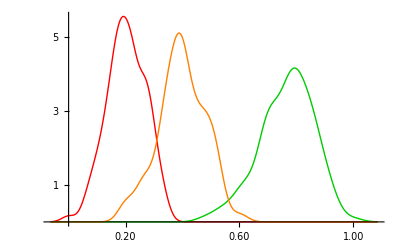

```mathematica
SmoothHistogram[
{tetrasimL,tetrasimA,tetrasimM}[[All,All,3]],
PlotStyle->$ConeColors[[1;;3]]]
```

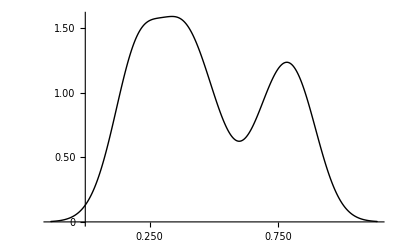

```mathematica
SmoothHistogram[
Flatten[{tetrasimL,tetrasimA,tetrasimM}[[All,All,3]]],
PlotStyle->Black]
```